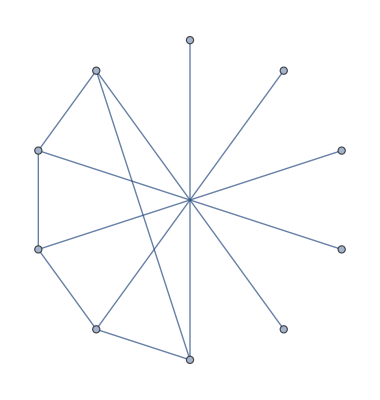

```mathematica
exp=EdgeAdd[CycleGraph[5],Table[i<->i+5,{i,1,5}]]
```

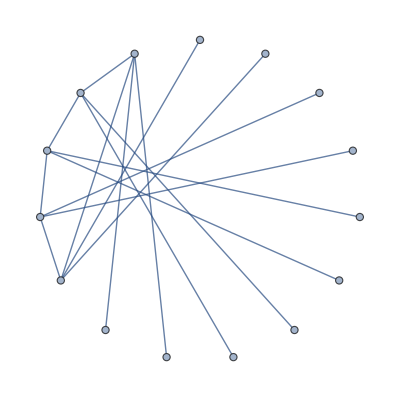

```mathematica
expDouble=EdgeAdd[CycleGraph[5],Flatten[Table[{i<->i+5,i<->i+10},{i,1,5}]]]
```

```mathematica
ToVars2[g_, pre_]:=Block[{exp,sep,vertex, vertices,var,var1, var2,  edges, edgeIndex, edge},
exp= "Solve[";
sep="";
vertices=VertexList[g];
For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> "Element["<>var<>", Integers]";
sep=" && " 
];

For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> "(1<="<>var<>" <=4)";
sep=" && " 
];

edges=EdgeList[g];

exp= exp<>sep<> pre;(* "x1 == 1 && x2== 2 && x3==3";*)
sep=" && " ;

For[edgeIndex=1,edgeIndex≤Length[edges],edgeIndex++,
edge=edges[[edgeIndex]];
var1 ="x" <> ToString[ edge[[1]] ];
var2 ="x" <> ToString[ edge[[2]] ];
exp= exp<>sep<> var1<>"!="<>var2;
sep=" && " 
];
exp=exp <> ", {";
sep="";
For[vertex=1,vertex<=Length[vertices], vertex++,
var ="x" <> ToString[ vertices[[vertex]] ];
exp= exp<>sep<> var;
sep=", " 
];
exp=exp <> "}]";
Return[Read[ StringToStream[ exp],Expression]]
]
```

```mathematica
CountSolutions[g_,edges1_,edges2_,edge3_, n_]:=Block[{ass, per,i,sols,result2,keys,edgeSet={edges1,edges2,edge3}, other,constr, temp, result3},
ass=Association[];
constr=NumberToConstraint[n];
sols=ToVars2[g,constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]={}
];
sols=ToVars2[EdgeAdd[g,edges1],constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]=Append[ass[per[[i]]],1]
];
sols=ToVars2[EdgeAdd[g,edges2],constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]=Append[ass[per[[i]]],2]
];
sols=ToVars2[EdgeAdd[g,edge3],constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]=Append[ass[per[[i]]],3]
];
result2={};
keys=Keys[ass];
For[i=1,i≤Length[keys],i++,
AppendTo[result2,ass[keys[[i]]]]
];
temp=Sort[Tally[result2]];
result3={};
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={1}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={2}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={3}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={1,2}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={2,3}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={1,3}&]]];
result3=Map[If[#=={},0,First[#]]&,result3];
{ n,IntegerDigits[n,4,5]+1,result3}
]
```

```mathematica
NumberToConstraint[val_]:=Block[
{n=IntegerDigits[val,4,5],res, sep=""},
res="";
Table[res=res<>sep<>"x"<>ToString[i+5]<>"=="<>ToString[n[[i]]+1]; sep = " && ",{i,1,5}];
res]
```

```mathematica
NumberToConstraint2[val_]:=Block[
{n=IntegerDigits[val,4,10],res, sep=""},
res="";
Table[res=res<>sep<>"x"<>ToString[i+5]<>"=="<>ToString[n[[i]]+1]; sep = " && ",{i,1,10}];
res]
```

```mathematica
CountSolutions2[g_,edges1_,edges2_,edge3_, n_]:=Block[{ass, per,i,sols,result2,keys,edgeSet={edges1,edges2,edge3}, other,constr, temp, result3},
ass=Association[];
constr=NumberToConstraint2[n];
sols=ToVars2[g,constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]={}
];
sols=ToVars2[EdgeAdd[g,edges1],constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]=Append[ass[per[[i]]],1]
];
sols=ToVars2[EdgeAdd[g,edges2],constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]=Append[ass[per[[i]]],2]
];
sols=ToVars2[EdgeAdd[g,edge3],constr];
per=Map[Map[Last[#]&,#]&,sols];
For[i=1,i<=Length[per],i++,
ass[per[[i]]]=Append[ass[per[[i]]],3]
];
result2={};
keys=Keys[ass];
For[i=1,i≤Length[keys],i++,
AppendTo[result2,ass[keys[[i]]]]
];
temp=Sort[Tally[result2]];
result3={};
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={1}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={2}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={3}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={1,2}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={2,3}&]]];
AppendTo[result3,Map[#[[2]]&,Select[temp,#[[1]]=={1,3}&]]];
result3=Map[If[#=={},0,First[#]]&,result3];
{ n,IntegerDigits[n,4,10]+1,result3}
]
```

```mathematica
NumberToConstraint[123]
```

x7==1 && x8==2 && x9==4 && x10==3 && x11==4

```mathematica
NumberToConstraint2[123]
```

x6==1 && x7==1 && x8==1 && x9==1 && x10==1 && x11==1 && x12==2 && x13==4 && x14==3 && x15==4

```mathematica
FromDigits[{1,2,3,4,2},4]
```

450

```mathematica
TableForm[
Monitor[
Table[CountSolutions[exp,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k],{k,0,1023}],k], TableDepth->2
]
```

0 | {1,1,1,1,1} | {6,6,18,0,0,0}
1 | {1,1,1,1,2} | {4,4,18,0,12,6}
2 | {1,1,1,1,3} | {4,4,18,0,12,6}
3 | {1,1,1,1,4} | {4,4,18,0,12,6}
4 | {1,1,1,2,1} | {4,4,18,6,6,6}
5 | {1,1,1,2,2} | {2,2,14,4,12,8}
6 | {1,1,1,2,3} | {3,3,17,4,12,8}
7 | {1,1,1,2,4} | {3,3,17,4,12,8}
8 | {1,1,1,3,1} | {4,4,18,6,6,6}
9 | {1,1,1,3,2} | {3,3,17,4,12,8}
10 | {1,1,1,3,3} | {2,2,14,4,12,8}
11 | {1,1,1,3,4} | {3,3,17,4,12,8}
12 | {1,1,1,4,1} | {4,4,18,6,6,6}
13 | {1,1,1,4,2} | {3,3,17,4,12,8}
14 | {1,1,1,4,3} | {3,3,17,4,12,8}
15 | {1,1,1,4,4} | {2,2,14,4,12,8}
16 | {1,1,2,1,1} | {4,4,18,0,6,12}
17 | {1,1,2,1,2} | {10,10,14,6,12,12}
18 | {1,1,2,1,3} | {8,8,17,6,12,12}
19 | {1,1,2,1,4} | {8,8,17,6,12,12}
20 | {1,1,2,2,1} | {2,2,14,4,8,12}
21 | {1,1,2,2,2} | {6,6,6,8,8,8}
22 | {1,1,2,2,3} | {5,5,14,6,10,11}
23 | {1,1,2,2,4} | {5,5,14,6,10,11}
24 | {1,1,2,3,1} | {3,3,17,4,8,12}
25 | {1,1,2,3,2} | {7,7,14,8,11,11}
26 | {1,1,2,3,3} | {5,5,14,6,11,10}
27 | {1,1,2,3,4} | {6,6,15,6,12,12}
28 | {1,1,2,4,1} | {3,3,17,4,8,12}
29 | {1,1,2,4,2} | {7,7,14,8,11,11}
30 | {1,1,2,4,3} | {6,6,15,6,12,12}
31 | {1,1,2,4,4} | {5,5,14,6,11,10}
32 | {1,1,3,1,1} | {4,4,18,0,6,12}
33 | {1,1,3,1,2} | {8,8,17,6,12,12}
34 | {1,1,3,1,3} | {10,10,14,6,12,12}
35 | {1,1,3,1,4} | {8,8,17,6,12,12}
36 | {1,1,3,2,1} | {3,3,17,4,8,12}
37 | {1,1,3,2,2} | {5,5,14,6,11,10}
38 | {1,1,3,2,3} | {7,7,14,8,11,11}
39 | {1,1,3,2,4} | {6,6,15,6,12,12}
40 | {1,1,3,3,1} | {2,2,14,4,8,12}
41 | {1,1,3,3,2} | {5,5,14,6,10,11}
42 | {1,1,3,3,3} | {6,6,6,8,8,8}
43 | {1,1,3,3,4} | {5,5,14,6,10,11}
44 | {1,1,3,4,1} | {3,3,17,4,8,12}
45 | {1,1,3,4,2} | {6,6,15,6,12,12}
46 | {1,1,3,4,3} | {7,7,14,8,11,11}
47 | {1,1,3,4,4} | {5,5,14,6,11,10}
48 | {1,1,4,1,1} | {4,4,18,0,6,12}
49 | {1,1,4,1,2} | {8,8,17,6,12,12}
50 | {1,1,4,1,3} | {8,8,17,6,12,12}
51 | {1,1,4,1,4} | {10,10,14,6,12,12}
52 | {1,1,4,2,1} | {3,3,17,4,8,12}
53 | {1,1,4,2,2} | {5,5,14,6,11,10}
54 | {1,1,4,2,3} | {6,6,15,6,12,12}
55 | {1,1,4,2,4} | {7,7,14,8,11,11}
56 | {1,1,4,3,1} | {3,3,17,4,8,12}
57 | {1,1,4,3,2} | {6,6,15,6,12,12}
58 | {1,1,4,3,3} | {5,5,14,6,11,10}
59 | {1,1,4,3,4} | {7,7,14,8,11,11}
60 | {1,1,4,4,1} | {2,2,14,4,8,12}
61 | {1,1,4,4,2} | {5,5,14,6,10,11}
62 | {1,1,4,4,3} | {5,5,14,6,10,11}
63 | {1,1,4,4,4} | {6,6,6,8,8,8}
64 | {1,2,1,1,1} | {4,10,12,6,12,0}
65 | {1,2,1,1,2} | {2,6,26,4,16,10}
66 | {1,2,1,1,3} | {3,7,23,4,16,10}
67 | {1,2,1,1,4} | {3,7,23,4,16,10}
68 | {1,2,1,2,1} | {10,6,18,8,12,10}
69 | {1,2,1,2,2} | {6,2,26,4,10,16}
70 | {1,2,1,2,3} | {7,5,23,6,13,14}
71 | {1,2,1,2,4} | {7,5,23,6,13,14}
72 | {1,2,1,3,1} | {8,7,18,8,12,10}
73 | {1,2,1,3,2} | {5,5,25,5,14,14}
74 | {1,2,1,3,3} | {5,4,19,5,13,12}
75 | {1,2,1,3,4} | {6,5,22,6,15,12}
76 | {1,2,1,4,1} | {8,7,18,8,12,10}
77 | {1,2,1,4,2} | {5,5,25,5,14,14}
78 | {1,2,1,4,3} | {6,5,22,6,15,12}
79 | {1,2,1,4,4} | {5,4,19,5,13,12}
80 | {1,2,2,1,1} | {2,6,10,4,12,8}
81 | {1,2,2,1,2} | {6,10,18,8,10,12}
82 | {1,2,2,1,3} | {5,7,16,6,13,11}
83 | {1,2,2,1,4} | {5,7,16,6,13,11}
84 | {1,2,2,2,1} | {6,2,10,4,8,12}
85 | {1,2,2,2,2} | {10,4,12,6,0,12}
86 | {1,2,2,2,3} | {7,3,13,4,8,12}
87 | {1,2,2,2,4} | {7,3,13,4,8,12}
88 | {1,2,2,3,1} | {5,5,14,5,11,11}
89 | {1,2,2,3,2} | {7,8,18,8,10,12}
90 | {1,2,2,3,3} | {4,5,15,5,12,10}
91 | {1,2,2,3,4} | {5,6,16,6,12,12}
92 | {1,2,2,4,1} | {5,5,14,5,11,11}
93 | {1,2,2,4,2} | {7,8,18,8,10,12}
94 | {1,2,2,4,3} | {5,6,16,6,12,12}
95 | {1,2,2,4,4} | {4,5,15,5,12,10}
96 | {1,2,3,1,1} | {3,7,13,4,12,8}
97 | {1,2,3,1,2} | {5,7,23,6,14,13}
98 | {1,2,3,1,3} | {7,11,17,8,13,12}
99 | {1,2,3,1,4} | {6,8,19,6,15,12}
100 | {1,2,3,2,1} | {7,5,16,6,11,13}
101 | {1,2,3,2,2} | {7,3,23,4,10,16}
102 | {1,2,3,2,3} | {11,7,17,8,12,13}
103 | {1,2,3,2,4} | {8,6,19,6,12,15}
104 | {1,2,3,3,1} | {5,4,15,5,10,12}
105 | {1,2,3,3,2} | {4,5,19,5,12,13}
106 | {1,2,3,3,3} | {7,7,9,8,8,8}
107 | {1,2,3,3,4} | {5,5,17,6,12,12}
108 | {1,2,3,4,1} | {6,5,16,6,12,12}
109 | {1,2,3,4,2} | {5,6,22,6,12,15}
110 | {1,2,3,4,3} | {8,8,17,9,12,12}
111 | {1,2,3,4,4} | {5,5,17,6,12,12}
112 | {1,2,4,1,1} | {3,7,13,4,12,8}
113 | {1,2,4,1,2} | {5,7,23,6,14,13}
114 | {1,2,4,1,3} | {6,8,19,6,15,12}
115 | {1,2,4,1,4} | {7,11,17,8,13,12}
116 | {1,2,4,2,1} | {7,5,16,6,11,13}
117 | {1,2,4,2,2} | {7,3,23,4,10,16}
118 | {1,2,4,2,3} | {8,6,19,6,12,15}
119 | {1,2,4,2,4} | {11,7,17,8,12,13}
120 | {1,2,4,3,1} | {6,5,16,6,12,12}
121 | {1,2,4,3,2} | {5,6,22,6,12,15}
122 | {1,2,4,3,3} | {5,5,17,6,12,12}
123 | {1,2,4,3,4} | {8,8,17,9,12,12}
124 | {1,2,4,4,1} | {5,4,15,5,10,12}
125 | {1,2,4,4,2} | {4,5,19,5,12,13}
126 | {1,2,4,4,3} | {5,5,17,6,12,12}
127 | {1,2,4,4,4} | {7,7,9,8,8,8}
128 | {1,3,1,1,1} | {4,10,12,6,12,0}
129 | {1,3,1,1,2} | {3,7,23,4,16,10}
130 | {1,3,1,1,3} | {2,6,26,4,16,10}
131 | {1,3,1,1,4} | {3,7,23,4,16,10}
132 | {1,3,1,2,1} | {8,7,18,8,12,10}
133 | {1,3,1,2,2} | {5,4,19,5,13,12}
134 | {1,3,1,2,3} | {5,5,25,5,14,14}
135 | {1,3,1,2,4} | {6,5,22,6,15,12}
136 | {1,3,1,3,1} | {10,6,18,8,12,10}
137 | {1,3,1,3,2} | {7,5,23,6,13,14}
138 | {1,3,1,3,3} | {6,2,26,4,10,16}
139 | {1,3,1,3,4} | {7,5,23,6,13,14}
140 | {1,3,1,4,1} | {8,7,18,8,12,10}
141 | {1,3,1,4,2} | {6,5,22,6,15,12}
142 | {1,3,1,4,3} | {5,5,25,5,14,14}
143 | {1,3,1,4,4} | {5,4,19,5,13,12}
144 | {1,3,2,1,1} | {3,7,13,4,12,8}
145 | {1,3,2,1,2} | {7,11,17,8,13,12}
146 | {1,3,2,1,3} | {5,7,23,6,14,13}
147 | {1,3,2,1,4} | {6,8,19,6,15,12}
148 | {1,3,2,2,1} | {5,4,15,5,10,12}
149 | {1,3,2,2,2} | {7,7,9,8,8,8}
150 | {1,3,2,2,3} | {4,5,19,5,12,13}
151 | {1,3,2,2,4} | {5,5,17,6,12,12}
152 | {1,3,2,3,1} | {7,5,16,6,11,13}
153 | {1,3,2,3,2} | {11,7,17,8,12,13}
154 | {1,3,2,3,3} | {7,3,23,4,10,16}
155 | {1,3,2,3,4} | {8,6,19,6,12,15}
156 | {1,3,2,4,1} | {6,5,16,6,12,12}
157 | {1,3,2,4,2} | {8,8,17,9,12,12}
158 | {1,3,2,4,3} | {5,6,22,6,12,15}
159 | {1,3,2,4,4} | {5,5,17,6,12,12}
160 | {1,3,3,1,1} | {2,6,10,4,12,8}
161 | {1,3,3,1,2} | {5,7,16,6,13,11}
162 | {1,3,3,1,3} | {6,10,18,8,10,12}
163 | {1,3,3,1,4} | {5,7,16,6,13,11}
164 | {1,3,3,2,1} | {5,5,14,5,11,11}
165 | {1,3,3,2,2} | {4,5,15,5,12,10}
166 | {1,3,3,2,3} | {7,8,18,8,10,12}
167 | {1,3,3,2,4} | {5,6,16,6,12,12}
168 | {1,3,3,3,1} | {6,2,10,4,8,12}
169 | {1,3,3,3,2} | {7,3,13,4,8,12}
170 | {1,3,3,3,3} | {10,4,12,6,0,12}
171 | {1,3,3,3,4} | {7,3,13,4,8,12}
172 | {1,3,3,4,1} | {5,5,14,5,11,11}
173 | {1,3,3,4,2} | {5,6,16,6,12,12}
174 | {1,3,3,4,3} | {7,8,18,8,10,12}
175 | {1,3,3,4,4} | {4,5,15,5,12,10}
176 | {1,3,4,1,1} | {3,7,13,4,12,8}
177 | {1,3,4,1,2} | {6,8,19,6,15,12}
178 | {1,3,4,1,3} | {5,7,23,6,14,13}
179 | {1,3,4,1,4} | {7,11,17,8,13,12}
180 | {1,3,4,2,1} | {6,5,16,6,12,12}
181 | {1,3,4,2,2} | {5,5,17,6,12,12}
182 | {1,3,4,2,3} | {5,6,22,6,12,15}
183 | {1,3,4,2,4} | {8,8,17,9,12,12}
184 | {1,3,4,3,1} | {7,5,16,6,11,13}
185 | {1,3,4,3,2} | {8,6,19,6,12,15}
186 | {1,3,4,3,3} | {7,3,23,4,10,16}
187 | {1,3,4,3,4} | {11,7,17,8,12,13}
188 | {1,3,4,4,1} | {5,4,15,5,10,12}
189 | {1,3,4,4,2} | {5,5,17,6,12,12}
190 | {1,3,4,4,3} | {4,5,19,5,12,13}
191 | {1,3,4,4,4} | {7,7,9,8,8,8}
192 | {1,4,1,1,1} | {4,10,12,6,12,0}
193 | {1,4,1,1,2} | {3,7,23,4,16,10}
194 | {1,4,1,1,3} | {3,7,23,4,16,10}
195 | {1,4,1,1,4} | {2,6,26,4,16,10}
196 | {1,4,1,2,1} | {8,7,18,8,12,10}
197 | {1,4,1,2,2} | {5,4,19,5,13,12}
198 | {1,4,1,2,3} | {6,5,22,6,15,12}
199 | {1,4,1,2,4} | {5,5,25,5,14,14}
200 | {1,4,1,3,1} | {8,7,18,8,12,10}
201 | {1,4,1,3,2} | {6,5,22,6,15,12}
202 | {1,4,1,3,3} | {5,4,19,5,13,12}
203 | {1,4,1,3,4} | {5,5,25,5,14,14}
204 | {1,4,1,4,1} | {10,6,18,8,12,10}
205 | {1,4,1,4,2} | {7,5,23,6,13,14}
206 | {1,4,1,4,3} | {7,5,23,6,13,14}
207 | {1,4,1,4,4} | {6,2,26,4,10,16}
208 | {1,4,2,1,1} | {3,7,13,4,12,8}
209 | {1,4,2,1,2} | {7,11,17,8,13,12}
210 | {1,4,2,1,3} | {6,8,19,6,15,12}
211 | {1,4,2,1,4} | {5,7,23,6,14,13}
212 | {1,4,2,2,1} | {5,4,15,5,10,12}
213 | {1,4,2,2,2} | {7,7,9,8,8,8}
214 | {1,4,2,2,3} | {5,5,17,6,12,12}
215 | {1,4,2,2,4} | {4,5,19,5,12,13}
216 | {1,4,2,3,1} | {6,5,16,6,12,12}
217 | {1,4,2,3,2} | {8,8,17,9,12,12}
218 | {1,4,2,3,3} | {5,5,17,6,12,12}
219 | {1,4,2,3,4} | {5,6,22,6,12,15}
220 | {1,4,2,4,1} | {7,5,16,6,11,13}
221 | {1,4,2,4,2} | {11,7,17,8,12,13}
222 | {1,4,2,4,3} | {8,6,19,6,12,15}
223 | {1,4,2,4,4} | {7,3,23,4,10,16}
224 | {1,4,3,1,1} | {3,7,13,4,12,8}
225 | {1,4,3,1,2} | {6,8,19,6,15,12}
226 | {1,4,3,1,3} | {7,11,17,8,13,12}
227 | {1,4,3,1,4} | {5,7,23,6,14,13}
228 | {1,4,3,2,1} | {6,5,16,6,12,12}
229 | {1,4,3,2,2} | {5,5,17,6,12,12}
230 | {1,4,3,2,3} | {8,8,17,9,12,12}
231 | {1,4,3,2,4} | {5,6,22,6,12,15}
232 | {1,4,3,3,1} | {5,4,15,5,10,12}
233 | {1,4,3,3,2} | {5,5,17,6,12,12}
234 | {1,4,3,3,3} | {7,7,9,8,8,8}
235 | {1,4,3,3,4} | {4,5,19,5,12,13}
236 | {1,4,3,4,1} | {7,5,16,6,11,13}
237 | {1,4,3,4,2} | {8,6,19,6,12,15}
238 | {1,4,3,4,3} | {11,7,17,8,12,13}
239 | {1,4,3,4,4} | {7,3,23,4,10,16}
240 | {1,4,4,1,1} | {2,6,10,4,12,8}
241 | {1,4,4,1,2} | {5,7,16,6,13,11}
242 | {1,4,4,1,3} | {5,7,16,6,13,11}
243 | {1,4,4,1,4} | {6,10,18,8,10,12}
244 | {1,4,4,2,1} | {5,5,14,5,11,11}
245 | {1,4,4,2,2} | {4,5,15,5,12,10}
246 | {1,4,4,2,3} | {5,6,16,6,12,12}
247 | {1,4,4,2,4} | {7,8,18,8,10,12}
248 | {1,4,4,3,1} | {5,5,14,5,11,11}
249 | {1,4,4,3,2} | {5,6,16,6,12,12}
250 | {1,4,4,3,3} | {4,5,15,5,12,10}
251 | {1,4,4,3,4} | {7,8,18,8,10,12}
252 | {1,4,4,4,1} | {6,2,10,4,8,12}
253 | {1,4,4,4,2} | {7,3,13,4,8,12}
254 | {1,4,4,4,3} | {7,3,13,4,8,12}
255 | {1,4,4,4,4} | {10,4,12,6,0,12}
256 | {2,1,1,1,1} | {10,4,12,6,0,12}
257 | {2,1,1,1,2} | {6,2,10,4,8,12}
258 | {2,1,1,1,3} | {7,3,13,4,8,12}
259 | {2,1,1,1,4} | {7,3,13,4,8,12}
260 | {2,1,1,2,1} | {6,10,18,8,10,12}
261 | {2,1,1,2,2} | {2,6,10,4,12,8}
262 | {2,1,1,2,3} | {5,7,16,6,13,11}
263 | {2,1,1,2,4} | {5,7,16,6,13,11}
264 | {2,1,1,3,1} | {7,8,18,8,10,12}
265 | {2,1,1,3,2} | {5,5,14,5,11,11}
266 | {2,1,1,3,3} | {4,5,15,5,12,10}
267 | {2,1,1,3,4} | {5,6,16,6,12,12}
268 | {2,1,1,4,1} | {7,8,18,8,10,12}
269 | {2,1,1,4,2} | {5,5,14,5,11,11}
270 | {2,1,1,4,3} | {5,6,16,6,12,12}
271 | {2,1,1,4,4} | {4,5,15,5,12,10}
272 | {2,1,2,1,1} | {6,2,26,4,10,16}
273 | {2,1,2,1,2} | {10,6,18,8,12,10}
274 | {2,1,2,1,3} | {7,5,23,6,13,14}
275 | {2,1,2,1,4} | {7,5,23,6,13,14}
276 | {2,1,2,2,1} | {2,6,26,4,16,10}
277 | {2,1,2,2,2} | {4,10,12,6,12,0}
278 | {2,1,2,2,3} | {3,7,23,4,16,10}
279 | {2,1,2,2,4} | {3,7,23,4,16,10}
280 | {2,1,2,3,1} | {5,5,25,5,14,14}
281 | {2,1,2,3,2} | {8,7,18,8,12,10}
282 | {2,1,2,3,3} | {5,4,19,5,13,12}
283 | {2,1,2,3,4} | {6,5,22,6,15,12}
284 | {2,1,2,4,1} | {5,5,25,5,14,14}
285 | {2,1,2,4,2} | {8,7,18,8,12,10}
286 | {2,1,2,4,3} | {6,5,22,6,15,12}
287 | {2,1,2,4,4} | {5,4,19,5,13,12}
288 | {2,1,3,1,1} | {7,3,23,4,10,16}
289 | {2,1,3,1,2} | {7,5,16,6,11,13}
290 | {2,1,3,1,3} | {11,7,17,8,12,13}
291 | {2,1,3,1,4} | {8,6,19,6,12,15}
292 | {2,1,3,2,1} | {5,7,23,6,14,13}
293 | {2,1,3,2,2} | {3,7,13,4,12,8}
294 | {2,1,3,2,3} | {7,11,17,8,13,12}
295 | {2,1,3,2,4} | {6,8,19,6,15,12}
296 | {2,1,3,3,1} | {4,5,19,5,12,13}
297 | {2,1,3,3,2} | {5,4,15,5,10,12}
298 | {2,1,3,3,3} | {7,7,9,8,8,8}
299 | {2,1,3,3,4} | {5,5,17,6,12,12}
300 | {2,1,3,4,1} | {5,6,22,6,12,15}
301 | {2,1,3,4,2} | {6,5,16,6,12,12}
302 | {2,1,3,4,3} | {8,8,17,9,12,12}
303 | {2,1,3,4,4} | {5,5,17,6,12,12}
304 | {2,1,4,1,1} | {7,3,23,4,10,16}
305 | {2,1,4,1,2} | {7,5,16,6,11,13}
306 | {2,1,4,1,3} | {8,6,19,6,12,15}
307 | {2,1,4,1,4} | {11,7,17,8,12,13}
308 | {2,1,4,2,1} | {5,7,23,6,14,13}
309 | {2,1,4,2,2} | {3,7,13,4,12,8}
310 | {2,1,4,2,3} | {6,8,19,6,15,12}
311 | {2,1,4,2,4} | {7,11,17,8,13,12}
312 | {2,1,4,3,1} | {5,6,22,6,12,15}
313 | {2,1,4,3,2} | {6,5,16,6,12,12}
314 | {2,1,4,3,3} | {5,5,17,6,12,12}
315 | {2,1,4,3,4} | {8,8,17,9,12,12}
316 | {2,1,4,4,1} | {4,5,19,5,12,13}
317 | {2,1,4,4,2} | {5,4,15,5,10,12}
318 | {2,1,4,4,3} | {5,5,17,6,12,12}
319 | {2,1,4,4,4} | {7,7,9,8,8,8}
320 | {2,2,1,1,1} | {6,6,6,8,8,8}
321 | {2,2,1,1,2} | {2,2,14,4,8,12}
322 | {2,2,1,1,3} | {5,5,14,6,10,11}
323 | {2,2,1,1,4} | {5,5,14,6,10,11}
324 | {2,2,1,2,1} | {10,10,14,6,12,12}
325 | {2,2,1,2,2} | {4,4,18,0,6,12}
326 | {2,2,1,2,3} | {8,8,17,6,12,12}
327 | {2,2,1,2,4} | {8,8,17,6,12,12}
328 | {2,2,1,3,1} | {7,7,14,8,11,11}
329 | {2,2,1,3,2} | {3,3,17,4,8,12}
330 | {2,2,1,3,3} | {5,5,14,6,11,10}
331 | {2,2,1,3,4} | {6,6,15,6,12,12}
332 | {2,2,1,4,1} | {7,7,14,8,11,11}
333 | {2,2,1,4,2} | {3,3,17,4,8,12}
334 | {2,2,1,4,3} | {6,6,15,6,12,12}
335 | {2,2,1,4,4} | {5,5,14,6,11,10}
336 | {2,2,2,1,1} | {2,2,14,4,12,8}
337 | {2,2,2,1,2} | {4,4,18,6,6,6}
338 | {2,2,2,1,3} | {3,3,17,4,12,8}
339 | {2,2,2,1,4} | {3,3,17,4,12,8}
340 | {2,2,2,2,1} | {4,4,18,0,12,6}
341 | {2,2,2,2,2} | {6,6,18,0,0,0}
342 | {2,2,2,2,3} | {4,4,18,0,12,6}
343 | {2,2,2,2,4} | {4,4,18,0,12,6}
344 | {2,2,2,3,1} | {3,3,17,4,12,8}
345 | {2,2,2,3,2} | {4,4,18,6,6,6}
346 | {2,2,2,3,3} | {2,2,14,4,12,8}
347 | {2,2,2,3,4} | {3,3,17,4,12,8}
348 | {2,2,2,4,1} | {3,3,17,4,12,8}
349 | {2,2,2,4,2} | {4,4,18,6,6,6}
350 | {2,2,2,4,3} | {3,3,17,4,12,8}
351 | {2,2,2,4,4} | {2,2,14,4,12,8}
352 | {2,2,3,1,1} | {5,5,14,6,11,10}
353 | {2,2,3,1,2} | {3,3,17,4,8,12}
354 | {2,2,3,1,3} | {7,7,14,8,11,11}
355 | {2,2,3,1,4} | {6,6,15,6,12,12}
356 | {2,2,3,2,1} | {8,8,17,6,12,12}
357 | {2,2,3,2,2} | {4,4,18,0,6,12}
358 | {2,2,3,2,3} | {10,10,14,6,12,12}
359 | {2,2,3,2,4} | {8,8,17,6,12,12}
360 | {2,2,3,3,1} | {5,5,14,6,10,11}
361 | {2,2,3,3,2} | {2,2,14,4,8,12}
362 | {2,2,3,3,3} | {6,6,6,8,8,8}
363 | {2,2,3,3,4} | {5,5,14,6,10,11}
364 | {2,2,3,4,1} | {6,6,15,6,12,12}
365 | {2,2,3,4,2} | {3,3,17,4,8,12}
366 | {2,2,3,4,3} | {7,7,14,8,11,11}
367 | {2,2,3,4,4} | {5,5,14,6,11,10}
368 | {2,2,4,1,1} | {5,5,14,6,11,10}
369 | {2,2,4,1,2} | {3,3,17,4,8,12}
370 | {2,2,4,1,3} | {6,6,15,6,12,12}
371 | {2,2,4,1,4} | {7,7,14,8,11,11}
372 | {2,2,4,2,1} | {8,8,17,6,12,12}
373 | {2,2,4,2,2} | {4,4,18,0,6,12}
374 | {2,2,4,2,3} | {8,8,17,6,12,12}
375 | {2,2,4,2,4} | {10,10,14,6,12,12}
376 | {2,2,4,3,1} | {6,6,15,6,12,12}
377 | {2,2,4,3,2} | {3,3,17,4,8,12}
378 | {2,2,4,3,3} | {5,5,14,6,11,10}
379 | {2,2,4,3,4} | {7,7,14,8,11,11}
380 | {2,2,4,4,1} | {5,5,14,6,10,11}
381 | {2,2,4,4,2} | {2,2,14,4,8,12}
382 | {2,2,4,4,3} | {5,5,14,6,10,11}
383 | {2,2,4,4,4} | {6,6,6,8,8,8}
384 | {2,3,1,1,1} | {7,7,9,8,8,8}
385 | {2,3,1,1,2} | {5,4,15,5,10,12}
386 | {2,3,1,1,3} | {4,5,19,5,12,13}
387 | {2,3,1,1,4} | {5,5,17,6,12,12}
388 | {2,3,1,2,1} | {7,11,17,8,13,12}
389 | {2,3,1,2,2} | {3,7,13,4,12,8}
390 | {2,3,1,2,3} | {5,7,23,6,14,13}
391 | {2,3,1,2,4} | {6,8,19,6,15,12}
392 | {2,3,1,3,1} | {11,7,17,8,12,13}
393 | {2,3,1,3,2} | {7,5,16,6,11,13}
394 | {2,3,1,3,3} | {7,3,23,4,10,16}
395 | {2,3,1,3,4} | {8,6,19,6,12,15}
396 | {2,3,1,4,1} | {8,8,17,9,12,12}
397 | {2,3,1,4,2} | {6,5,16,6,12,12}
398 | {2,3,1,4,3} | {5,6,22,6,12,15}
399 | {2,3,1,4,4} | {5,5,17,6,12,12}
400 | {2,3,2,1,1} | {5,4,19,5,13,12}
401 | {2,3,2,1,2} | {8,7,18,8,12,10}
402 | {2,3,2,1,3} | {5,5,25,5,14,14}
403 | {2,3,2,1,4} | {6,5,22,6,15,12}
404 | {2,3,2,2,1} | {3,7,23,4,16,10}
405 | {2,3,2,2,2} | {4,10,12,6,12,0}
406 | {2,3,2,2,3} | {2,6,26,4,16,10}
407 | {2,3,2,2,4} | {3,7,23,4,16,10}
408 | {2,3,2,3,1} | {7,5,23,6,13,14}
409 | {2,3,2,3,2} | {10,6,18,8,12,10}
410 | {2,3,2,3,3} | {6,2,26,4,10,16}
411 | {2,3,2,3,4} | {7,5,23,6,13,14}
412 | {2,3,2,4,1} | {6,5,22,6,15,12}
413 | {2,3,2,4,2} | {8,7,18,8,12,10}
414 | {2,3,2,4,3} | {5,5,25,5,14,14}
415 | {2,3,2,4,4} | {5,4,19,5,13,12}
416 | {2,3,3,1,1} | {4,5,15,5,12,10}
417 | {2,3,3,1,2} | {5,5,14,5,11,11}
418 | {2,3,3,1,3} | {7,8,18,8,10,12}
419 | {2,3,3,1,4} | {5,6,16,6,12,12}
420 | {2,3,3,2,1} | {5,7,16,6,13,11}
421 | {2,3,3,2,2} | {2,6,10,4,12,8}
422 | {2,3,3,2,3} | {6,10,18,8,10,12}
423 | {2,3,3,2,4} | {5,7,16,6,13,11}
424 | {2,3,3,3,1} | {7,3,13,4,8,12}
425 | {2,3,3,3,2} | {6,2,10,4,8,12}
426 | {2,3,3,3,3} | {10,4,12,6,0,12}
427 | {2,3,3,3,4} | {7,3,13,4,8,12}
428 | {2,3,3,4,1} | {5,6,16,6,12,12}
429 | {2,3,3,4,2} | {5,5,14,5,11,11}
430 | {2,3,3,4,3} | {7,8,18,8,10,12}
431 | {2,3,3,4,4} | {4,5,15,5,12,10}
432 | {2,3,4,1,1} | {5,5,17,6,12,12}
433 | {2,3,4,1,2} | {6,5,16,6,12,12}
434 | {2,3,4,1,3} | {5,6,22,6,12,15}
435 | {2,3,4,1,4} | {8,8,17,9,12,12}
436 | {2,3,4,2,1} | {6,8,19,6,15,12}
437 | {2,3,4,2,2} | {3,7,13,4,12,8}
438 | {2,3,4,2,3} | {5,7,23,6,14,13}
439 | {2,3,4,2,4} | {7,11,17,8,13,12}
440 | {2,3,4,3,1} | {8,6,19,6,12,15}
441 | {2,3,4,3,2} | {7,5,16,6,11,13}
442 | {2,3,4,3,3} | {7,3,23,4,10,16}
443 | {2,3,4,3,4} | {11,7,17,8,12,13}
444 | {2,3,4,4,1} | {5,5,17,6,12,12}
445 | {2,3,4,4,2} | {5,4,15,5,10,12}
446 | {2,3,4,4,3} | {4,5,19,5,12,13}
447 | {2,3,4,4,4} | {7,7,9,8,8,8}
448 | {2,4,1,1,1} | {7,7,9,8,8,8}
449 | {2,4,1,1,2} | {5,4,15,5,10,12}
450 | {2,4,1,1,3} | {5,5,17,6,12,12}
451 | {2,4,1,1,4} | {4,5,19,5,12,13}
452 | {2,4,1,2,1} | {7,11,17,8,13,12}
453 | {2,4,1,2,2} | {3,7,13,4,12,8}
454 | {2,4,1,2,3} | {6,8,19,6,15,12}
455 | {2,4,1,2,4} | {5,7,23,6,14,13}
456 | {2,4,1,3,1} | {8,8,17,9,12,12}
457 | {2,4,1,3,2} | {6,5,16,6,12,12}
458 | {2,4,1,3,3} | {5,5,17,6,12,12}
459 | {2,4,1,3,4} | {5,6,22,6,12,15}
460 | {2,4,1,4,1} | {11,7,17,8,12,13}
461 | {2,4,1,4,2} | {7,5,16,6,11,13}
462 | {2,4,1,4,3} | {8,6,19,6,12,15}
463 | {2,4,1,4,4} | {7,3,23,4,10,16}
464 | {2,4,2,1,1} | {5,4,19,5,13,12}
465 | {2,4,2,1,2} | {8,7,18,8,12,10}
466 | {2,4,2,1,3} | {6,5,22,6,15,12}
467 | {2,4,2,1,4} | {5,5,25,5,14,14}
468 | {2,4,2,2,1} | {3,7,23,4,16,10}
469 | {2,4,2,2,2} | {4,10,12,6,12,0}
470 | {2,4,2,2,3} | {3,7,23,4,16,10}
471 | {2,4,2,2,4} | {2,6,26,4,16,10}
472 | {2,4,2,3,1} | {6,5,22,6,15,12}
473 | {2,4,2,3,2} | {8,7,18,8,12,10}
474 | {2,4,2,3,3} | {5,4,19,5,13,12}
475 | {2,4,2,3,4} | {5,5,25,5,14,14}
476 | {2,4,2,4,1} | {7,5,23,6,13,14}
477 | {2,4,2,4,2} | {10,6,18,8,12,10}
478 | {2,4,2,4,3} | {7,5,23,6,13,14}
479 | {2,4,2,4,4} | {6,2,26,4,10,16}
480 | {2,4,3,1,1} | {5,5,17,6,12,12}
481 | {2,4,3,1,2} | {6,5,16,6,12,12}
482 | {2,4,3,1,3} | {8,8,17,9,12,12}
483 | {2,4,3,1,4} | {5,6,22,6,12,15}
484 | {2,4,3,2,1} | {6,8,19,6,15,12}
485 | {2,4,3,2,2} | {3,7,13,4,12,8}
486 | {2,4,3,2,3} | {7,11,17,8,13,12}
487 | {2,4,3,2,4} | {5,7,23,6,14,13}
488 | {2,4,3,3,1} | {5,5,17,6,12,12}
489 | {2,4,3,3,2} | {5,4,15,5,10,12}
490 | {2,4,3,3,3} | {7,7,9,8,8,8}
491 | {2,4,3,3,4} | {4,5,19,5,12,13}
492 | {2,4,3,4,1} | {8,6,19,6,12,15}
493 | {2,4,3,4,2} | {7,5,16,6,11,13}
494 | {2,4,3,4,3} | {11,7,17,8,12,13}
495 | {2,4,3,4,4} | {7,3,23,4,10,16}
496 | {2,4,4,1,1} | {4,5,15,5,12,10}
497 | {2,4,4,1,2} | {5,5,14,5,11,11}
498 | {2,4,4,1,3} | {5,6,16,6,12,12}
499 | {2,4,4,1,4} | {7,8,18,8,10,12}
500 | {2,4,4,2,1} | {5,7,16,6,13,11}
501 | {2,4,4,2,2} | {2,6,10,4,12,8}
502 | {2,4,4,2,3} | {5,7,16,6,13,11}
503 | {2,4,4,2,4} | {6,10,18,8,10,12}
504 | {2,4,4,3,1} | {5,6,16,6,12,12}
505 | {2,4,4,3,2} | {5,5,14,5,11,11}
506 | {2,4,4,3,3} | {4,5,15,5,12,10}
507 | {2,4,4,3,4} | {7,8,18,8,10,12}
508 | {2,4,4,4,1} | {7,3,13,4,8,12}
509 | {2,4,4,4,2} | {6,2,10,4,8,12}
510 | {2,4,4,4,3} | {7,3,13,4,8,12}
511 | {2,4,4,4,4} | {10,4,12,6,0,12}
512 | {3,1,1,1,1} | {10,4,12,6,0,12}
513 | {3,1,1,1,2} | {7,3,13,4,8,12}
514 | {3,1,1,1,3} | {6,2,10,4,8,12}
515 | {3,1,1,1,4} | {7,3,13,4,8,12}
516 | {3,1,1,2,1} | {7,8,18,8,10,12}
517 | {3,1,1,2,2} | {4,5,15,5,12,10}
518 | {3,1,1,2,3} | {5,5,14,5,11,11}
519 | {3,1,1,2,4} | {5,6,16,6,12,12}
520 | {3,1,1,3,1} | {6,10,18,8,10,12}
521 | {3,1,1,3,2} | {5,7,16,6,13,11}
522 | {3,1,1,3,3} | {2,6,10,4,12,8}
523 | {3,1,1,3,4} | {5,7,16,6,13,11}
524 | {3,1,1,4,1} | {7,8,18,8,10,12}
525 | {3,1,1,4,2} | {5,6,16,6,12,12}
526 | {3,1,1,4,3} | {5,5,14,5,11,11}
527 | {3,1,1,4,4} | {4,5,15,5,12,10}
528 | {3,1,2,1,1} | {7,3,23,4,10,16}
529 | {3,1,2,1,2} | {11,7,17,8,12,13}
530 | {3,1,2,1,3} | {7,5,16,6,11,13}
531 | {3,1,2,1,4} | {8,6,19,6,12,15}
532 | {3,1,2,2,1} | {4,5,19,5,12,13}
533 | {3,1,2,2,2} | {7,7,9,8,8,8}
534 | {3,1,2,2,3} | {5,4,15,5,10,12}
535 | {3,1,2,2,4} | {5,5,17,6,12,12}
536 | {3,1,2,3,1} | {5,7,23,6,14,13}
537 | {3,1,2,3,2} | {7,11,17,8,13,12}
538 | {3,1,2,3,3} | {3,7,13,4,12,8}
539 | {3,1,2,3,4} | {6,8,19,6,15,12}
540 | {3,1,2,4,1} | {5,6,22,6,12,15}
541 | {3,1,2,4,2} | {8,8,17,9,12,12}
542 | {3,1,2,4,3} | {6,5,16,6,12,12}
543 | {3,1,2,4,4} | {5,5,17,6,12,12}
544 | {3,1,3,1,1} | {6,2,26,4,10,16}
545 | {3,1,3,1,2} | {7,5,23,6,13,14}
546 | {3,1,3,1,3} | {10,6,18,8,12,10}
547 | {3,1,3,1,4} | {7,5,23,6,13,14}
548 | {3,1,3,2,1} | {5,5,25,5,14,14}
549 | {3,1,3,2,2} | {5,4,19,5,13,12}
550 | {3,1,3,2,3} | {8,7,18,8,12,10}
551 | {3,1,3,2,4} | {6,5,22,6,15,12}
552 | {3,1,3,3,1} | {2,6,26,4,16,10}
553 | {3,1,3,3,2} | {3,7,23,4,16,10}
554 | {3,1,3,3,3} | {4,10,12,6,12,0}
555 | {3,1,3,3,4} | {3,7,23,4,16,10}
556 | {3,1,3,4,1} | {5,5,25,5,14,14}
557 | {3,1,3,4,2} | {6,5,22,6,15,12}
558 | {3,1,3,4,3} | {8,7,18,8,12,10}
559 | {3,1,3,4,4} | {5,4,19,5,13,12}
560 | {3,1,4,1,1} | {7,3,23,4,10,16}
561 | {3,1,4,1,2} | {8,6,19,6,12,15}
562 | {3,1,4,1,3} | {7,5,16,6,11,13}
563 | {3,1,4,1,4} | {11,7,17,8,12,13}
564 | {3,1,4,2,1} | {5,6,22,6,12,15}
565 | {3,1,4,2,2} | {5,5,17,6,12,12}
566 | {3,1,4,2,3} | {6,5,16,6,12,12}
567 | {3,1,4,2,4} | {8,8,17,9,12,12}
568 | {3,1,4,3,1} | {5,7,23,6,14,13}
569 | {3,1,4,3,2} | {6,8,19,6,15,12}
570 | {3,1,4,3,3} | {3,7,13,4,12,8}
571 | {3,1,4,3,4} | {7,11,17,8,13,12}
572 | {3,1,4,4,1} | {4,5,19,5,12,13}
573 | {3,1,4,4,2} | {5,5,17,6,12,12}
574 | {3,1,4,4,3} | {5,4,15,5,10,12}
575 | {3,1,4,4,4} | {7,7,9,8,8,8}
576 | {3,2,1,1,1} | {7,7,9,8,8,8}
577 | {3,2,1,1,2} | {4,5,19,5,12,13}
578 | {3,2,1,1,3} | {5,4,15,5,10,12}
579 | {3,2,1,1,4} | {5,5,17,6,12,12}
580 | {3,2,1,2,1} | {11,7,17,8,12,13}
581 | {3,2,1,2,2} | {7,3,23,4,10,16}
582 | {3,2,1,2,3} | {7,5,16,6,11,13}
583 | {3,2,1,2,4} | {8,6,19,6,12,15}
584 | {3,2,1,3,1} | {7,11,17,8,13,12}
585 | {3,2,1,3,2} | {5,7,23,6,14,13}
586 | {3,2,1,3,3} | {3,7,13,4,12,8}
587 | {3,2,1,3,4} | {6,8,19,6,15,12}
588 | {3,2,1,4,1} | {8,8,17,9,12,12}
589 | {3,2,1,4,2} | {5,6,22,6,12,15}
590 | {3,2,1,4,3} | {6,5,16,6,12,12}
591 | {3,2,1,4,4} | {5,5,17,6,12,12}
592 | {3,2,2,1,1} | {4,5,15,5,12,10}
593 | {3,2,2,1,2} | {7,8,18,8,10,12}
594 | {3,2,2,1,3} | {5,5,14,5,11,11}
595 | {3,2,2,1,4} | {5,6,16,6,12,12}
596 | {3,2,2,2,1} | {7,3,13,4,8,12}
597 | {3,2,2,2,2} | {10,4,12,6,0,12}
598 | {3,2,2,2,3} | {6,2,10,4,8,12}
599 | {3,2,2,2,4} | {7,3,13,4,8,12}
600 | {3,2,2,3,1} | {5,7,16,6,13,11}
601 | {3,2,2,3,2} | {6,10,18,8,10,12}
602 | {3,2,2,3,3} | {2,6,10,4,12,8}
603 | {3,2,2,3,4} | {5,7,16,6,13,11}
604 | {3,2,2,4,1} | {5,6,16,6,12,12}
605 | {3,2,2,4,2} | {7,8,18,8,10,12}
606 | {3,2,2,4,3} | {5,5,14,5,11,11}
607 | {3,2,2,4,4} | {4,5,15,5,12,10}
608 | {3,2,3,1,1} | {5,4,19,5,13,12}
609 | {3,2,3,1,2} | {5,5,25,5,14,14}
610 | {3,2,3,1,3} | {8,7,18,8,12,10}
611 | {3,2,3,1,4} | {6,5,22,6,15,12}
612 | {3,2,3,2,1} | {7,5,23,6,13,14}
613 | {3,2,3,2,2} | {6,2,26,4,10,16}
614 | {3,2,3,2,3} | {10,6,18,8,12,10}
615 | {3,2,3,2,4} | {7,5,23,6,13,14}
616 | {3,2,3,3,1} | {3,7,23,4,16,10}
617 | {3,2,3,3,2} | {2,6,26,4,16,10}
618 | {3,2,3,3,3} | {4,10,12,6,12,0}
619 | {3,2,3,3,4} | {3,7,23,4,16,10}
620 | {3,2,3,4,1} | {6,5,22,6,15,12}
621 | {3,2,3,4,2} | {5,5,25,5,14,14}
622 | {3,2,3,4,3} | {8,7,18,8,12,10}
623 | {3,2,3,4,4} | {5,4,19,5,13,12}
624 | {3,2,4,1,1} | {5,5,17,6,12,12}
625 | {3,2,4,1,2} | {5,6,22,6,12,15}
626 | {3,2,4,1,3} | {6,5,16,6,12,12}
627 | {3,2,4,1,4} | {8,8,17,9,12,12}
628 | {3,2,4,2,1} | {8,6,19,6,12,15}
629 | {3,2,4,2,2} | {7,3,23,4,10,16}
630 | {3,2,4,2,3} | {7,5,16,6,11,13}
631 | {3,2,4,2,4} | {11,7,17,8,12,13}
632 | {3,2,4,3,1} | {6,8,19,6,15,12}
633 | {3,2,4,3,2} | {5,7,23,6,14,13}
634 | {3,2,4,3,3} | {3,7,13,4,12,8}
635 | {3,2,4,3,4} | {7,11,17,8,13,12}
636 | {3,2,4,4,1} | {5,5,17,6,12,12}
637 | {3,2,4,4,2} | {4,5,19,5,12,13}
638 | {3,2,4,4,3} | {5,4,15,5,10,12}
639 | {3,2,4,4,4} | {7,7,9,8,8,8}
640 | {3,3,1,1,1} | {6,6,6,8,8,8}
641 | {3,3,1,1,2} | {5,5,14,6,10,11}
642 | {3,3,1,1,3} | {2,2,14,4,8,12}
643 | {3,3,1,1,4} | {5,5,14,6,10,11}
644 | {3,3,1,2,1} | {7,7,14,8,11,11}
645 | {3,3,1,2,2} | {5,5,14,6,11,10}
646 | {3,3,1,2,3} | {3,3,17,4,8,12}
647 | {3,3,1,2,4} | {6,6,15,6,12,12}
648 | {3,3,1,3,1} | {10,10,14,6,12,12}
649 | {3,3,1,3,2} | {8,8,17,6,12,12}
650 | {3,3,1,3,3} | {4,4,18,0,6,12}
651 | {3,3,1,3,4} | {8,8,17,6,12,12}
652 | {3,3,1,4,1} | {7,7,14,8,11,11}
653 | {3,3,1,4,2} | {6,6,15,6,12,12}
654 | {3,3,1,4,3} | {3,3,17,4,8,12}
655 | {3,3,1,4,4} | {5,5,14,6,11,10}
656 | {3,3,2,1,1} | {5,5,14,6,11,10}
657 | {3,3,2,1,2} | {7,7,14,8,11,11}
658 | {3,3,2,1,3} | {3,3,17,4,8,12}
659 | {3,3,2,1,4} | {6,6,15,6,12,12}
660 | {3,3,2,2,1} | {5,5,14,6,10,11}
661 | {3,3,2,2,2} | {6,6,6,8,8,8}
662 | {3,3,2,2,3} | {2,2,14,4,8,12}
663 | {3,3,2,2,4} | {5,5,14,6,10,11}
664 | {3,3,2,3,1} | {8,8,17,6,12,12}
665 | {3,3,2,3,2} | {10,10,14,6,12,12}
666 | {3,3,2,3,3} | {4,4,18,0,6,12}
667 | {3,3,2,3,4} | {8,8,17,6,12,12}
668 | {3,3,2,4,1} | {6,6,15,6,12,12}
669 | {3,3,2,4,2} | {7,7,14,8,11,11}
670 | {3,3,2,4,3} | {3,3,17,4,8,12}
671 | {3,3,2,4,4} | {5,5,14,6,11,10}
672 | {3,3,3,1,1} | {2,2,14,4,12,8}
673 | {3,3,3,1,2} | {3,3,17,4,12,8}
674 | {3,3,3,1,3} | {4,4,18,6,6,6}
675 | {3,3,3,1,4} | {3,3,17,4,12,8}
676 | {3,3,3,2,1} | {3,3,17,4,12,8}
677 | {3,3,3,2,2} | {2,2,14,4,12,8}
678 | {3,3,3,2,3} | {4,4,18,6,6,6}
679 | {3,3,3,2,4} | {3,3,17,4,12,8}
680 | {3,3,3,3,1} | {4,4,18,0,12,6}
681 | {3,3,3,3,2} | {4,4,18,0,12,6}
682 | {3,3,3,3,3} | {6,6,18,0,0,0}
683 | {3,3,3,3,4} | {4,4,18,0,12,6}
684 | {3,3,3,4,1} | {3,3,17,4,12,8}
685 | {3,3,3,4,2} | {3,3,17,4,12,8}
686 | {3,3,3,4,3} | {4,4,18,6,6,6}
687 | {3,3,3,4,4} | {2,2,14,4,12,8}
688 | {3,3,4,1,1} | {5,5,14,6,11,10}
689 | {3,3,4,1,2} | {6,6,15,6,12,12}
690 | {3,3,4,1,3} | {3,3,17,4,8,12}
691 | {3,3,4,1,4} | {7,7,14,8,11,11}
692 | {3,3,4,2,1} | {6,6,15,6,12,12}
693 | {3,3,4,2,2} | {5,5,14,6,11,10}
694 | {3,3,4,2,3} | {3,3,17,4,8,12}
695 | {3,3,4,2,4} | {7,7,14,8,11,11}
696 | {3,3,4,3,1} | {8,8,17,6,12,12}
697 | {3,3,4,3,2} | {8,8,17,6,12,12}
698 | {3,3,4,3,3} | {4,4,18,0,6,12}
699 | {3,3,4,3,4} | {10,10,14,6,12,12}
700 | {3,3,4,4,1} | {5,5,14,6,10,11}
701 | {3,3,4,4,2} | {5,5,14,6,10,11}
702 | {3,3,4,4,3} | {2,2,14,4,8,12}
703 | {3,3,4,4,4} | {6,6,6,8,8,8}
704 | {3,4,1,1,1} | {7,7,9,8,8,8}
705 | {3,4,1,1,2} | {5,5,17,6,12,12}
706 | {3,4,1,1,3} | {5,4,15,5,10,12}
707 | {3,4,1,1,4} | {4,5,19,5,12,13}
708 | {3,4,1,2,1} | {8,8,17,9,12,12}
709 | {3,4,1,2,2} | {5,5,17,6,12,12}
710 | {3,4,1,2,3} | {6,5,16,6,12,12}
711 | {3,4,1,2,4} | {5,6,22,6,12,15}
712 | {3,4,1,3,1} | {7,11,17,8,13,12}
713 | {3,4,1,3,2} | {6,8,19,6,15,12}
714 | {3,4,1,3,3} | {3,7,13,4,12,8}
715 | {3,4,1,3,4} | {5,7,23,6,14,13}
716 | {3,4,1,4,1} | {11,7,17,8,12,13}
717 | {3,4,1,4,2} | {8,6,19,6,12,15}
718 | {3,4,1,4,3} | {7,5,16,6,11,13}
719 | {3,4,1,4,4} | {7,3,23,4,10,16}
720 | {3,4,2,1,1} | {5,5,17,6,12,12}
721 | {3,4,2,1,2} | {8,8,17,9,12,12}
722 | {3,4,2,1,3} | {6,5,16,6,12,12}
723 | {3,4,2,1,4} | {5,6,22,6,12,15}
724 | {3,4,2,2,1} | {5,5,17,6,12,12}
725 | {3,4,2,2,2} | {7,7,9,8,8,8}
726 | {3,4,2,2,3} | {5,4,15,5,10,12}
727 | {3,4,2,2,4} | {4,5,19,5,12,13}
728 | {3,4,2,3,1} | {6,8,19,6,15,12}
729 | {3,4,2,3,2} | {7,11,17,8,13,12}
730 | {3,4,2,3,3} | {3,7,13,4,12,8}
731 | {3,4,2,3,4} | {5,7,23,6,14,13}
732 | {3,4,2,4,1} | {8,6,19,6,12,15}
733 | {3,4,2,4,2} | {11,7,17,8,12,13}
734 | {3,4,2,4,3} | {7,5,16,6,11,13}
735 | {3,4,2,4,4} | {7,3,23,4,10,16}
736 | {3,4,3,1,1} | {5,4,19,5,13,12}
737 | {3,4,3,1,2} | {6,5,22,6,15,12}
738 | {3,4,3,1,3} | {8,7,18,8,12,10}
739 | {3,4,3,1,4} | {5,5,25,5,14,14}
740 | {3,4,3,2,1} | {6,5,22,6,15,12}
741 | {3,4,3,2,2} | {5,4,19,5,13,12}
742 | {3,4,3,2,3} | {8,7,18,8,12,10}
743 | {3,4,3,2,4} | {5,5,25,5,14,14}
744 | {3,4,3,3,1} | {3,7,23,4,16,10}
745 | {3,4,3,3,2} | {3,7,23,4,16,10}
746 | {3,4,3,3,3} | {4,10,12,6,12,0}
747 | {3,4,3,3,4} | {2,6,26,4,16,10}
748 | {3,4,3,4,1} | {7,5,23,6,13,14}
749 | {3,4,3,4,2} | {7,5,23,6,13,14}
750 | {3,4,3,4,3} | {10,6,18,8,12,10}
751 | {3,4,3,4,4} | {6,2,26,4,10,16}
752 | {3,4,4,1,1} | {4,5,15,5,12,10}
753 | {3,4,4,1,2} | {5,6,16,6,12,12}
754 | {3,4,4,1,3} | {5,5,14,5,11,11}
755 | {3,4,4,1,4} | {7,8,18,8,10,12}
756 | {3,4,4,2,1} | {5,6,16,6,12,12}
757 | {3,4,4,2,2} | {4,5,15,5,12,10}
758 | {3,4,4,2,3} | {5,5,14,5,11,11}
759 | {3,4,4,2,4} | {7,8,18,8,10,12}
760 | {3,4,4,3,1} | {5,7,16,6,13,11}
761 | {3,4,4,3,2} | {5,7,16,6,13,11}
762 | {3,4,4,3,3} | {2,6,10,4,12,8}
763 | {3,4,4,3,4} | {6,10,18,8,10,12}
764 | {3,4,4,4,1} | {7,3,13,4,8,12}
765 | {3,4,4,4,2} | {7,3,13,4,8,12}
766 | {3,4,4,4,3} | {6,2,10,4,8,12}
767 | {3,4,4,4,4} | {10,4,12,6,0,12}
768 | {4,1,1,1,1} | {10,4,12,6,0,12}
769 | {4,1,1,1,2} | {7,3,13,4,8,12}
770 | {4,1,1,1,3} | {7,3,13,4,8,12}
771 | {4,1,1,1,4} | {6,2,10,4,8,12}
772 | {4,1,1,2,1} | {7,8,18,8,10,12}
773 | {4,1,1,2,2} | {4,5,15,5,12,10}
774 | {4,1,1,2,3} | {5,6,16,6,12,12}
775 | {4,1,1,2,4} | {5,5,14,5,11,11}
776 | {4,1,1,3,1} | {7,8,18,8,10,12}
777 | {4,1,1,3,2} | {5,6,16,6,12,12}
778 | {4,1,1,3,3} | {4,5,15,5,12,10}
779 | {4,1,1,3,4} | {5,5,14,5,11,11}
780 | {4,1,1,4,1} | {6,10,18,8,10,12}
781 | {4,1,1,4,2} | {5,7,16,6,13,11}
782 | {4,1,1,4,3} | {5,7,16,6,13,11}
783 | {4,1,1,4,4} | {2,6,10,4,12,8}
784 | {4,1,2,1,1} | {7,3,23,4,10,16}
785 | {4,1,2,1,2} | {11,7,17,8,12,13}
786 | {4,1,2,1,3} | {8,6,19,6,12,15}
787 | {4,1,2,1,4} | {7,5,16,6,11,13}
788 | {4,1,2,2,1} | {4,5,19,5,12,13}
789 | {4,1,2,2,2} | {7,7,9,8,8,8}
790 | {4,1,2,2,3} | {5,5,17,6,12,12}
791 | {4,1,2,2,4} | {5,4,15,5,10,12}
792 | {4,1,2,3,1} | {5,6,22,6,12,15}
793 | {4,1,2,3,2} | {8,8,17,9,12,12}
794 | {4,1,2,3,3} | {5,5,17,6,12,12}
795 | {4,1,2,3,4} | {6,5,16,6,12,12}
796 | {4,1,2,4,1} | {5,7,23,6,14,13}
797 | {4,1,2,4,2} | {7,11,17,8,13,12}
798 | {4,1,2,4,3} | {6,8,19,6,15,12}
799 | {4,1,2,4,4} | {3,7,13,4,12,8}
800 | {4,1,3,1,1} | {7,3,23,4,10,16}
801 | {4,1,3,1,2} | {8,6,19,6,12,15}
802 | {4,1,3,1,3} | {11,7,17,8,12,13}
803 | {4,1,3,1,4} | {7,5,16,6,11,13}
804 | {4,1,3,2,1} | {5,6,22,6,12,15}
805 | {4,1,3,2,2} | {5,5,17,6,12,12}
806 | {4,1,3,2,3} | {8,8,17,9,12,12}
807 | {4,1,3,2,4} | {6,5,16,6,12,12}
808 | {4,1,3,3,1} | {4,5,19,5,12,13}
809 | {4,1,3,3,2} | {5,5,17,6,12,12}
810 | {4,1,3,3,3} | {7,7,9,8,8,8}
811 | {4,1,3,3,4} | {5,4,15,5,10,12}
812 | {4,1,3,4,1} | {5,7,23,6,14,13}
813 | {4,1,3,4,2} | {6,8,19,6,15,12}
814 | {4,1,3,4,3} | {7,11,17,8,13,12}
815 | {4,1,3,4,4} | {3,7,13,4,12,8}
816 | {4,1,4,1,1} | {6,2,26,4,10,16}
817 | {4,1,4,1,2} | {7,5,23,6,13,14}
818 | {4,1,4,1,3} | {7,5,23,6,13,14}
819 | {4,1,4,1,4} | {10,6,18,8,12,10}
820 | {4,1,4,2,1} | {5,5,25,5,14,14}
821 | {4,1,4,2,2} | {5,4,19,5,13,12}
822 | {4,1,4,2,3} | {6,5,22,6,15,12}
823 | {4,1,4,2,4} | {8,7,18,8,12,10}
824 | {4,1,4,3,1} | {5,5,25,5,14,14}
825 | {4,1,4,3,2} | {6,5,22,6,15,12}
826 | {4,1,4,3,3} | {5,4,19,5,13,12}
827 | {4,1,4,3,4} | {8,7,18,8,12,10}
828 | {4,1,4,4,1} | {2,6,26,4,16,10}
829 | {4,1,4,4,2} | {3,7,23,4,16,10}
830 | {4,1,4,4,3} | {3,7,23,4,16,10}
831 | {4,1,4,4,4} | {4,10,12,6,12,0}
832 | {4,2,1,1,1} | {7,7,9,8,8,8}
833 | {4,2,1,1,2} | {4,5,19,5,12,13}
834 | {4,2,1,1,3} | {5,5,17,6,12,12}
835 | {4,2,1,1,4} | {5,4,15,5,10,12}
836 | {4,2,1,2,1} | {11,7,17,8,12,13}
837 | {4,2,1,2,2} | {7,3,23,4,10,16}
838 | {4,2,1,2,3} | {8,6,19,6,12,15}
839 | {4,2,1,2,4} | {7,5,16,6,11,13}
840 | {4,2,1,3,1} | {8,8,17,9,12,12}
841 | {4,2,1,3,2} | {5,6,22,6,12,15}
842 | {4,2,1,3,3} | {5,5,17,6,12,12}
843 | {4,2,1,3,4} | {6,5,16,6,12,12}
844 | {4,2,1,4,1} | {7,11,17,8,13,12}
845 | {4,2,1,4,2} | {5,7,23,6,14,13}
846 | {4,2,1,4,3} | {6,8,19,6,15,12}
847 | {4,2,1,4,4} | {3,7,13,4,12,8}
848 | {4,2,2,1,1} | {4,5,15,5,12,10}
849 | {4,2,2,1,2} | {7,8,18,8,10,12}
850 | {4,2,2,1,3} | {5,6,16,6,12,12}
851 | {4,2,2,1,4} | {5,5,14,5,11,11}
852 | {4,2,2,2,1} | {7,3,13,4,8,12}
853 | {4,2,2,2,2} | {10,4,12,6,0,12}
854 | {4,2,2,2,3} | {7,3,13,4,8,12}
855 | {4,2,2,2,4} | {6,2,10,4,8,12}
856 | {4,2,2,3,1} | {5,6,16,6,12,12}
857 | {4,2,2,3,2} | {7,8,18,8,10,12}
858 | {4,2,2,3,3} | {4,5,15,5,12,10}
859 | {4,2,2,3,4} | {5,5,14,5,11,11}
860 | {4,2,2,4,1} | {5,7,16,6,13,11}
861 | {4,2,2,4,2} | {6,10,18,8,10,12}
862 | {4,2,2,4,3} | {5,7,16,6,13,11}
863 | {4,2,2,4,4} | {2,6,10,4,12,8}
864 | {4,2,3,1,1} | {5,5,17,6,12,12}
865 | {4,2,3,1,2} | {5,6,22,6,12,15}
866 | {4,2,3,1,3} | {8,8,17,9,12,12}
867 | {4,2,3,1,4} | {6,5,16,6,12,12}
868 | {4,2,3,2,1} | {8,6,19,6,12,15}
869 | {4,2,3,2,2} | {7,3,23,4,10,16}
870 | {4,2,3,2,3} | {11,7,17,8,12,13}
871 | {4,2,3,2,4} | {7,5,16,6,11,13}
872 | {4,2,3,3,1} | {5,5,17,6,12,12}
873 | {4,2,3,3,2} | {4,5,19,5,12,13}
874 | {4,2,3,3,3} | {7,7,9,8,8,8}
875 | {4,2,3,3,4} | {5,4,15,5,10,12}
876 | {4,2,3,4,1} | {6,8,19,6,15,12}
877 | {4,2,3,4,2} | {5,7,23,6,14,13}
878 | {4,2,3,4,3} | {7,11,17,8,13,12}
879 | {4,2,3,4,4} | {3,7,13,4,12,8}
880 | {4,2,4,1,1} | {5,4,19,5,13,12}
881 | {4,2,4,1,2} | {5,5,25,5,14,14}
882 | {4,2,4,1,3} | {6,5,22,6,15,12}
883 | {4,2,4,1,4} | {8,7,18,8,12,10}
884 | {4,2,4,2,1} | {7,5,23,6,13,14}
885 | {4,2,4,2,2} | {6,2,26,4,10,16}
886 | {4,2,4,2,3} | {7,5,23,6,13,14}
887 | {4,2,4,2,4} | {10,6,18,8,12,10}
888 | {4,2,4,3,1} | {6,5,22,6,15,12}
889 | {4,2,4,3,2} | {5,5,25,5,14,14}
890 | {4,2,4,3,3} | {5,4,19,5,13,12}
891 | {4,2,4,3,4} | {8,7,18,8,12,10}
892 | {4,2,4,4,1} | {3,7,23,4,16,10}
893 | {4,2,4,4,2} | {2,6,26,4,16,10}
894 | {4,2,4,4,3} | {3,7,23,4,16,10}
895 | {4,2,4,4,4} | {4,10,12,6,12,0}
896 | {4,3,1,1,1} | {7,7,9,8,8,8}
897 | {4,3,1,1,2} | {5,5,17,6,12,12}
898 | {4,3,1,1,3} | {4,5,19,5,12,13}
899 | {4,3,1,1,4} | {5,4,15,5,10,12}
900 | {4,3,1,2,1} | {8,8,17,9,12,12}
901 | {4,3,1,2,2} | {5,5,17,6,12,12}
902 | {4,3,1,2,3} | {5,6,22,6,12,15}
903 | {4,3,1,2,4} | {6,5,16,6,12,12}
904 | {4,3,1,3,1} | {11,7,17,8,12,13}
905 | {4,3,1,3,2} | {8,6,19,6,12,15}
906 | {4,3,1,3,3} | {7,3,23,4,10,16}
907 | {4,3,1,3,4} | {7,5,16,6,11,13}
908 | {4,3,1,4,1} | {7,11,17,8,13,12}
909 | {4,3,1,4,2} | {6,8,19,6,15,12}
910 | {4,3,1,4,3} | {5,7,23,6,14,13}
911 | {4,3,1,4,4} | {3,7,13,4,12,8}
912 | {4,3,2,1,1} | {5,5,17,6,12,12}
913 | {4,3,2,1,2} | {8,8,17,9,12,12}
914 | {4,3,2,1,3} | {5,6,22,6,12,15}
915 | {4,3,2,1,4} | {6,5,16,6,12,12}
916 | {4,3,2,2,1} | {5,5,17,6,12,12}
917 | {4,3,2,2,2} | {7,7,9,8,8,8}
918 | {4,3,2,2,3} | {4,5,19,5,12,13}
919 | {4,3,2,2,4} | {5,4,15,5,10,12}
920 | {4,3,2,3,1} | {8,6,19,6,12,15}
921 | {4,3,2,3,2} | {11,7,17,8,12,13}
922 | {4,3,2,3,3} | {7,3,23,4,10,16}
923 | {4,3,2,3,4} | {7,5,16,6,11,13}
924 | {4,3,2,4,1} | {6,8,19,6,15,12}
925 | {4,3,2,4,2} | {7,11,17,8,13,12}
926 | {4,3,2,4,3} | {5,7,23,6,14,13}
927 | {4,3,2,4,4} | {3,7,13,4,12,8}
928 | {4,3,3,1,1} | {4,5,15,5,12,10}
929 | {4,3,3,1,2} | {5,6,16,6,12,12}
930 | {4,3,3,1,3} | {7,8,18,8,10,12}
931 | {4,3,3,1,4} | {5,5,14,5,11,11}
932 | {4,3,3,2,1} | {5,6,16,6,12,12}
933 | {4,3,3,2,2} | {4,5,15,5,12,10}
934 | {4,3,3,2,3} | {7,8,18,8,10,12}
935 | {4,3,3,2,4} | {5,5,14,5,11,11}
936 | {4,3,3,3,1} | {7,3,13,4,8,12}
937 | {4,3,3,3,2} | {7,3,13,4,8,12}
938 | {4,3,3,3,3} | {10,4,12,6,0,12}
939 | {4,3,3,3,4} | {6,2,10,4,8,12}
940 | {4,3,3,4,1} | {5,7,16,6,13,11}
941 | {4,3,3,4,2} | {5,7,16,6,13,11}
942 | {4,3,3,4,3} | {6,10,18,8,10,12}
943 | {4,3,3,4,4} | {2,6,10,4,12,8}
944 | {4,3,4,1,1} | {5,4,19,5,13,12}
945 | {4,3,4,1,2} | {6,5,22,6,15,12}
946 | {4,3,4,1,3} | {5,5,25,5,14,14}
947 | {4,3,4,1,4} | {8,7,18,8,12,10}
948 | {4,3,4,2,1} | {6,5,22,6,15,12}
949 | {4,3,4,2,2} | {5,4,19,5,13,12}
950 | {4,3,4,2,3} | {5,5,25,5,14,14}
951 | {4,3,4,2,4} | {8,7,18,8,12,10}
952 | {4,3,4,3,1} | {7,5,23,6,13,14}
953 | {4,3,4,3,2} | {7,5,23,6,13,14}
954 | {4,3,4,3,3} | {6,2,26,4,10,16}
955 | {4,3,4,3,4} | {10,6,18,8,12,10}
956 | {4,3,4,4,1} | {3,7,23,4,16,10}
957 | {4,3,4,4,2} | {3,7,23,4,16,10}
958 | {4,3,4,4,3} | {2,6,26,4,16,10}
959 | {4,3,4,4,4} | {4,10,12,6,12,0}
960 | {4,4,1,1,1} | {6,6,6,8,8,8}
961 | {4,4,1,1,2} | {5,5,14,6,10,11}
962 | {4,4,1,1,3} | {5,5,14,6,10,11}
963 | {4,4,1,1,4} | {2,2,14,4,8,12}
964 | {4,4,1,2,1} | {7,7,14,8,11,11}
965 | {4,4,1,2,2} | {5,5,14,6,11,10}
966 | {4,4,1,2,3} | {6,6,15,6,12,12}
967 | {4,4,1,2,4} | {3,3,17,4,8,12}
968 | {4,4,1,3,1} | {7,7,14,8,11,11}
969 | {4,4,1,3,2} | {6,6,15,6,12,12}
970 | {4,4,1,3,3} | {5,5,14,6,11,10}
971 | {4,4,1,3,4} | {3,3,17,4,8,12}
972 | {4,4,1,4,1} | {10,10,14,6,12,12}
973 | {4,4,1,4,2} | {8,8,17,6,12,12}
974 | {4,4,1,4,3} | {8,8,17,6,12,12}
975 | {4,4,1,4,4} | {4,4,18,0,6,12}
976 | {4,4,2,1,1} | {5,5,14,6,11,10}
977 | {4,4,2,1,2} | {7,7,14,8,11,11}
978 | {4,4,2,1,3} | {6,6,15,6,12,12}
979 | {4,4,2,1,4} | {3,3,17,4,8,12}
980 | {4,4,2,2,1} | {5,5,14,6,10,11}
981 | {4,4,2,2,2} | {6,6,6,8,8,8}
982 | {4,4,2,2,3} | {5,5,14,6,10,11}
983 | {4,4,2,2,4} | {2,2,14,4,8,12}
984 | {4,4,2,3,1} | {6,6,15,6,12,12}
985 | {4,4,2,3,2} | {7,7,14,8,11,11}
986 | {4,4,2,3,3} | {5,5,14,6,11,10}
987 | {4,4,2,3,4} | {3,3,17,4,8,12}
988 | {4,4,2,4,1} | {8,8,17,6,12,12}
989 | {4,4,2,4,2} | {10,10,14,6,12,12}
990 | {4,4,2,4,3} | {8,8,17,6,12,12}
991 | {4,4,2,4,4} | {4,4,18,0,6,12}
992 | {4,4,3,1,1} | {5,5,14,6,11,10}
993 | {4,4,3,1,2} | {6,6,15,6,12,12}
994 | {4,4,3,1,3} | {7,7,14,8,11,11}
995 | {4,4,3,1,4} | {3,3,17,4,8,12}
996 | {4,4,3,2,1} | {6,6,15,6,12,12}
997 | {4,4,3,2,2} | {5,5,14,6,11,10}
998 | {4,4,3,2,3} | {7,7,14,8,11,11}
999 | {4,4,3,2,4} | {3,3,17,4,8,12}
1000 | {4,4,3,3,1} | {5,5,14,6,10,11}
1001 | {4,4,3,3,2} | {5,5,14,6,10,11}
1002 | {4,4,3,3,3} | {6,6,6,8,8,8}
1003 | {4,4,3,3,4} | {2,2,14,4,8,12}
1004 | {4,4,3,4,1} | {8,8,17,6,12,12}
1005 | {4,4,3,4,2} | {8,8,17,6,12,12}
1006 | {4,4,3,4,3} | {10,10,14,6,12,12}
1007 | {4,4,3,4,4} | {4,4,18,0,6,12}
1008 | {4,4,4,1,1} | {2,2,14,4,12,8}
1009 | {4,4,4,1,2} | {3,3,17,4,12,8}
1010 | {4,4,4,1,3} | {3,3,17,4,12,8}
1011 | {4,4,4,1,4} | {4,4,18,6,6,6}
1012 | {4,4,4,2,1} | {3,3,17,4,12,8}
1013 | {4,4,4,2,2} | {2,2,14,4,12,8}
1014 | {4,4,4,2,3} | {3,3,17,4,12,8}
1015 | {4,4,4,2,4} | {4,4,18,6,6,6}
1016 | {4,4,4,3,1} | {3,3,17,4,12,8}
1017 | {4,4,4,3,2} | {3,3,17,4,12,8}
1018 | {4,4,4,3,3} | {2,2,14,4,12,8}
1019 | {4,4,4,3,4} | {4,4,18,6,6,6}
1020 | {4,4,4,4,1} | {4,4,18,0,12,6}
1021 | {4,4,4,4,2} | {4,4,18,0,12,6}
1022 | {4,4,4,4,3} | {4,4,18,0,12,6}
1023 | {4,4,4,4,4} | {6,6,18,0,0,0}

```mathematica
NumberToConstraint[125]
```

x6==1 && x7==2 && x8==4 && x9==4 && x10==2

```mathematica
{125,{0,1,3,3,1},{{{1},4},{{2},5},{{3},19},{{1,2},5},{{1,3},13},{{2,3},12}}}
```

```mathematica
CountSolutions[exp,{1<->3,1<->4},{2<->4,2<->5},{3<->5},1023]
```

{1023,{4,4,4,4,4},{6,6,18,0,0,0}}

```mathematica
TableForm[
Monitor[
Table[CountSolutions2[expDouble,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k],{k,0,4096}],k], TableDepth->2
]
```

1
 |  |  |  |

$OutputSizeLimit::noout: This output cannot be updated because Out[500] has no value.

```mathematica
TableForm[
Monitor[
Table[CountSolutions2[expDouble,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k],{k,0,10}],k], TableDepth->2
]
```

0 | {1,1,1,1,1,1,1,1,1,1} | {6,6,18,0,0,0}
1 | {1,1,1,1,1,1,1,1,1,2} | {4,4,12,0,0,0}
2 | {1,1,1,1,1,1,1,1,1,3} | {4,4,12,0,0,0}
3 | {1,1,1,1,1,1,1,1,1,4} | {4,4,12,0,0,0}
4 | {1,1,1,1,1,1,1,1,2,1} | {4,4,12,0,0,0}
5 | {1,1,1,1,1,1,1,1,2,2} | {2,2,6,0,0,0}
6 | {1,1,1,1,1,1,1,1,2,3} | {3,3,9,0,0,0}
7 | {1,1,1,1,1,1,1,1,2,4} | {3,3,9,0,0,0}
8 | {1,1,1,1,1,1,1,1,3,1} | {4,4,12,0,0,0}
9 | {1,1,1,1,1,1,1,1,3,2} | {3,3,9,0,0,0}
10 | {1,1,1,1,1,1,1,1,3,3} | {2,2,6,0,0,0}

```mathematica
TableForm[
Monitor[
Table[CountSolutions2[expDouble,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k],{k,0,1000,3}],k], TableDepth->2
]
```

$Aborted

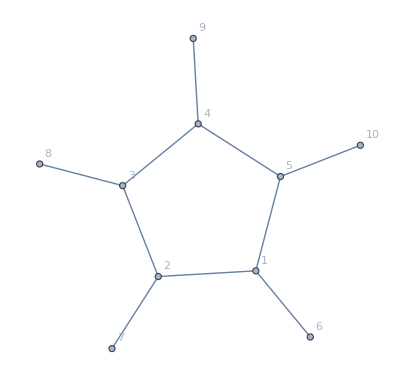

```mathematica
Graph[exp, GraphLayout->"SpringElectricalEmbedding", VertexLabels->"Name"]
```

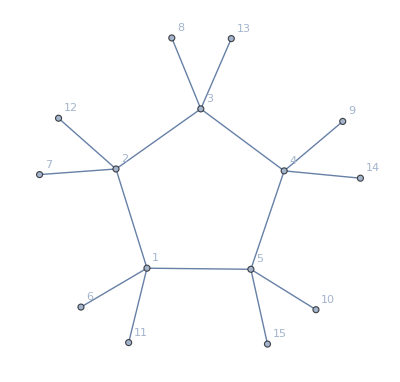

```mathematica
Graph[expDouble, GraphLayout->"SpringElectricalEmbedding", VertexLabels->"Name"]
```

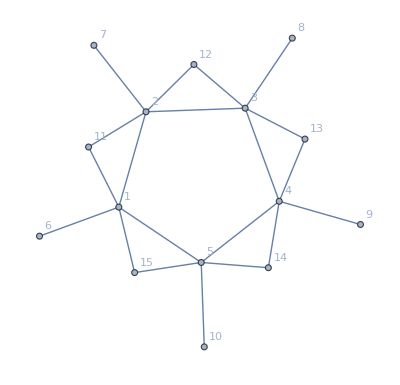

```mathematica
expMixed=Graph[EdgeAdd[CycleGraph[5],Flatten[
Table[{
i<->i+5,
Mod[i,5]+1<->i+10,
i<->i+10
},{i,1,5}]]],GraphLayout->"SpringElectricalEmbedding", VertexLabels->"Name"]
```

```mathematica
expMixed=Graph[EdgeAdd[CycleGraph[5],Flatten[
Table[{
i<->i+5,
Mod[i,5]+1<->i+10,
i+5<->i+10,
i<->i+10
},{i,1,5}]]],GraphLayout->"SpringElectricalEmbedding", VertexLabels->"Name"]
```

```mathematica
TableForm[
Monitor[
Table[CountSolutions2[expMixed,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k],{k,{10863,14697,35145,43452,45369,58788,70290,82431,105435,140580,173808,181476}}],k], TableDepth->2
]
```

10863 | {1,1,1,3,3,3,2,3,4,4} | {0,0,0,0,0,0}
14697 | {1,1,1,4,3,2,2,3,3,2} | {0,0,0,0,1,0}
35145 | {1,1,3,1,3,2,2,1,3,2} | {0,0,0,0,1,0}
43452 | {1,1,3,3,3,2,3,4,4,1} | {0,0,0,1,0,0}
45369 | {1,1,3,4,1,2,1,4,3,2} | {0,0,0,0,0,1}
58788 | {1,1,4,3,2,2,3,3,2,1} | {0,0,0,0,0,1}
70290 | {1,2,1,2,1,3,3,2,1,3} | {0,0,0,1,1,0}
82431 | {1,2,2,1,1,2,4,4,4,4} | {0,0,0,0,0,0}
105435 | {1,2,3,2,3,4,4,2,3,4} | {0,0,0,1,0,0}
140580 | {1,3,1,3,2,2,1,3,2,1} | {0,0,0,0,0,1}
173808 | {1,3,3,3,2,3,4,4,1,1} | {0,0,0,0,0,1}
181476 | {1,3,4,1,2,1,4,3,2,1} | {0,0,0,0,1,0}

```mathematica
TableForm[
Monitor[
Table[CountSolutions2[expMixed,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k],{k,1,100}],k], TableDepth->2
]
```

```mathematica
{{1, {1,1,1,1,1,1,1,1,1,2}, {2,2,6,0,0,0}}, {2, {1,1,1,1,1,1,1,1,1,3}, {2,2,6,0,0,0}}, {3, {1,1,1,1,1,1,1,1,1,4}, {2,2,6,0,0,0}}, {4, {1,1,1,1,1,1,1,1,2,1}, {2,2,6,0,0,0}}, {5, {1,1,1,1,1,1,1,1,2,2}, {0,2,2,0,0,0}}, {6, {1,1,1,1,1,1,1,1,2,3}, {1,0,2,0,0,0}}, {7, {1,1,1,1,1,1,1,1,2,4}, {1,0,2,0,0,0}}, {8, {1,1,1,1,1,1,1,1,3,1}, {2,2,6,0,0,0}}, {9, {1,1,1,1,1,1,1,1,3,2}, {1,0,2,0,0,0}}, {10, {1,1,1,1,1,1,1,1,3,3}, {0,2,2,0,0,0}}, {11, {1,1,1,1,1,1,1,1,3,4}, {1,0,2,0,0,0}}, {12, {1,1,1,1,1,1,1,1,4,1}, {2,2,6,0,0,0}}, {13, {1,1,1,1,1,1,1,1,4,2}, {1,0,2,0,0,0}}, {14, {1,1,1,1,1,1,1,1,4,3}, {1,0,2,0,0,0}}, {15, {1,1,1,1,1,1,1,1,4,4}, {0,2,2,0,0,0}}, {16, {1,1,1,1,1,1,1,2,1,1}, {2,2,6,0,0,0}}, {17, {1,1,1,1,1,1,1,2,1,2}, {0,2,0,0,0,0}}, {18, {1,1,1,1,1,1,1,2,1,3}, {1,0,3,0,0,0}}, {19, {1,1,1,1,1,1,1,2,1,4}, {1,0,3,0,0,0}}, {20, {1,1,1,1,1,1,1,2,2,1}, {2,2,0,0,0,0}}, {21, {1,1,1,1,1,1,1,2,2,2}, {0,2,0,0,0,0}}, {22, {1,1,1,1,1,1,1,2,2,3}, {1,0,0,0,0,0}}, {23, {1,1,1,1,1,1,1,2,2,4}, {1,0,0,0,0,0}}, {24, {1,1,1,1,1,1,1,2,3,1}, {0,0,3,0,0,0}}, {25, {1,1,1,1,1,1,1,2,3,2}, {0,0,0,0,0,0}}, {26, {1,1,1,1,1,1,1,2,3,3}, {0,0,1,0,0,0}}, {27, {1,1,1,1,1,1,1,2,3,4}, {0,0,2,0,0,0}}, {28, {1,1,1,1,1,1,1,2,4,1}, {0,0,3,0,0,0}}, {29, {1,1,1,1,1,1,1,2,4,2}, {0,0,0,0,0,0}}, {30, {1,1,1,1,1,1,1,2,4,3}, {0,0,2,0,0,0}}, {31, {1,1,1,1,1,1,1,2,4,4}, {0,0,1,0,0,0}}, {32, {1,1,1,1,1,1,1,3,1,1}, {2,2,6,0,0,0}}, {33, {1,1,1,1,1,1,1,3,1,2}, {1,0,3,0,0,0}}, {34, {1,1,1,1,1,1,1,3,1,3}, {0,2,0,0,0,0}}, {35, {1,1,1,1,1,1,1,3,1,4}, {1,0,3,0,0,0}}, {36, {1,1,1,1,1,1,1,3,2,1}, {0,0,3,0,0,0}}, {37, {1,1,1,1,1,1,1,3,2,2}, {0,0,1,0,0,0}}, {38, {1,1,1,1,1,1,1,3,2,3}, {0,0,0,0,0,0}}, {39, {1,1,1,1,1,1,1,3,2,4}, {0,0,2,0,0,0}}, {40, {1,1,1,1,1,1,1,3,3,1}, {2,2,0,0,0,0}}, {41, {1,1,1,1,1,1,1,3,3,2}, {1,0,0,0,0,0}}, {42, {1,1,1,1,1,1,1,3,3,3}, {0,2,0,0,0,0}}, {43, {1,1,1,1,1,1,1,3,3,4}, {1,0,0,0,0,0}}, {44, {1,1,1,1,1,1,1,3,4,1}, {0,0,3,0,0,0}}, {45, {1,1,1,1,1,1,1,3,4,2}, {0,0,2,0,0,0}}, {46, {1,1,1,1,1,1,1,3,4,3}, {0,0,0,0,0,0}}, {47, {1,1,1,1,1,1,1,3,4,4}, {0,0,1,0,0,0}}, {48, {1,1,1,1,1,1,1,4,1,1}, {2,2,6,0,0,0}}, {49, {1,1,1,1,1,1,1,4,1,2}, {1,0,3,0,0,0}}, {50, {1,1,1,1,1,1,1,4,1,3}, {1,0,3,0,0,0}}, {51, {1,1,1,1,1,1,1,4,1,4}, {0,2,0,0,0,0}}, {52, {1,1,1,1,1,1,1,4,2,1}, {0,0,3,0,0,0}}, {53, {1,1,1,1,1,1,1,4,2,2}, {0,0,1,0,0,0}}, {54, {1,1,1,1,1,1,1,4,2,3}, {0,0,2,0,0,0}}, {55, {1,1,1,1,1,1,1,4,2,4}, {0,0,0,0,0,0}}, {56, {1,1,1,1,1,1,1,4,3,1}, {0,0,3,0,0,0}}, {57, {1,1,1,1,1,1,1,4,3,2}, {0,0,2,0,0,0}}, {58, {1,1,1,1,1,1,1,4,3,3}, {0,0,1,0,0,0}}, {59, {1,1,1,1,1,1,1,4,3,4}, {0,0,0,0,0,0}}, {60, {1,1,1,1,1,1,1,4,4,1}, {2,2,0,0,0,0}}, {61, {1,1,1,1,1,1,1,4,4,2}, {1,0,0,0,0,0}}, {62, {1,1,1,1,1,1,1,4,4,3}, {1,0,0,0,0,0}}, {63, {1,1,1,1,1,1,1,4,4,4}, {0,2,0,0,0,0}}, {64, {1,1,1,1,1,1,2,1,1,1}, {2,2,6,0,0,0}}, {65, {1,1,1,1,1,1,2,1,1,2}, {0,0,2,0,0,0}}, {66, {1,1,1,1,1,1,2,1,1,3}, {1,1,2,0,0,0}}, {67, {1,1,1,1,1,1,2,1,1,4}, {1,1,2,0,0,0}}, {68, {1,1,1,1,1,1,2,1,2,1}, {2,0,0,0,0,0}}, {69, {1,1,1,1,1,1,2,1,2,2}, {0,0,0,0,0,0}}, {70, {1,1,1,1,1,1,2,1,2,3}, {1,0,0,0,0,0}}, {71, {1,1,1,1,1,1,2,1,2,4}, {1,0,0,0,0,0}}, {72, {1,1,1,1,1,1,2,1,3,1}, {0,1,3,0,0,0}}, {73, {1,1,1,1,1,1,2,1,3,2}, {0,0,1,0,0,0}}, {74, {1,1,1,1,1,1,2,1,3,3}, {0,1,1,0,0,0}}, {75, {1,1,1,1,1,1,2,1,3,4}, {0,0,1,0,0,0}}, {76, {1,1,1,1,1,1,2,1,4,1}, {0,1,3,0,0,0}}, {77, {1,1,1,1,1,1,2,1,4,2}, {0,0,1,0,0,0}}, {78, {1,1,1,1,1,1,2,1,4,3}, {0,0,1,0,0,0}}, {79, {1,1,1,1,1,1,2,1,4,4}, {0,1,1,0,0,0}}, {80, {1,1,1,1,1,1,2,2,1,1}, {2,0,2,0,0,0}}, {81, {1,1,1,1,1,1,2,2,1,2}, {0,0,0,0,0,0}}, {82, {1,1,1,1,1,1,2,2,1,3}, {1,0,1,0,0,0}}, {83, {1,1,1,1,1,1,2,2,1,4}, {1,0,1,0,0,0}}, {84, {1,1,1,1,1,1,2,2,2,1}, {2,0,0,0,0,0}}, {85, {1,1,1,1,1,1,2,2,2,2}, {0,0,0,0,0,0}}, {86, {1,1,1,1,1,1,2,2,2,3}, {1,0,0,0,0,0}}, {87, {1,1,1,1,1,1,2,2,2,4}, {1,0,0,0,0,0}}, {88, {1,1,1,1,1,1,2,2,3,1}, {0,0,1,0,0,0}}, {89, {1,1,1,1,1,1,2,2,3,2}, {0,0,0,0,0,0}}, {90, {1,1,1,1,1,1,2,2,3,3}, {0,0,0,0,0,0}}, {91, {1,1,1,1,1,1,2,2,3,4}, {0,0,1,0,0,0}}, {92, {1,1,1,1,1,1,2,2,4,1}, {0,0,1,0,0,0}}, {93, {1,1,1,1,1,1,2,2,4,2}, {0,0,0,0,0,0}}, {94, {1,1,1,1,1,1,2,2,4,3}, {0,0,1,0,0,0}}, {95, {1,1,1,1,1,1,2,2,4,4}, {0,0,0,0,0,0}}, {96, {1,1,1,1,1,1,2,3,1,1}, {0,1,2,0,0,0}}, {97, {1,1,1,1,1,1,2,3,1,2}, {0,0,1,0,0,0}}, {98, {1,1,1,1,1,1,2,3,1,3}, {0,1,0,0,0,0}}, {99, {1,1,1,1,1,1,2,3,1,4}, {0,0,1,0,0,0}}, {100, {1,1,1,1,1,1,2,3,2,1}, {0,0,0,0,0,0}}}
```

{{1,{1,1,1,1,1,1,1,1,1,2},{2,2,6,0,0,0}},{2,{1,1,1,1,1,1,1,1,1,3},{2,2,6,0,0,0}},{3,{1,1,1,1,1,1,1,1,1,4},{2,2,6,0,0,0}},{4,{1,1,1,1,1,1,1,1,2,1},{2,2,6,0,0,0}},{5,{1,1,1,1,1,1,1,1,2,2},{0,2,2,0,0,0}},{6,{1,1,1,1,1,1,1,1,2,3},{1,0,2,0,0,0}},{7,{1,1,1,1,1,1,1,1,2,4},{1,0,2,0,0,0}},{8,{1,1,1,1,1,1,1,1,3,1},{2,2,6,0,0,0}},{9,{1,1,1,1,1,1,1,1,3,2},{1,0,2,0,0,0}},{10,{1,1,1,1,1,1,1,1,3,3},{0,2,2,0,0,0}},{11,{1,1,1,1,1,1,1,1,3,4},{1,0,2,0,0,0}},{12,{1,1,1,1,1,1,1,1,4,1},{2,2,6,0,0,0}},{13,{1,1,1,1,1,1,1,1,4,2},{1,0,2,0,0,0}},{14,{1,1,1,1,1,1,1,1,4,3},{1,0,2,0,0,0}},{15,{1,1,1,1,1,1,1,1,4,4},{0,2,2,0,0,0}},{16,{1,1,1,1,1,1,1,2,1,1},{2,2,6,0,0,0}},{17,{1,1,1,1,1,1,1,2,1,2},{0,2,0,0,0,0}},{18,{1,1,1,1,1,1,1,2,1,3},{1,0,3,0,0,0}},{19,{1,1,1,1,1,1,1,2,1,4},{1,0,3,0,0,0}},{20,{1,1,1,1,1,1,1,2,2,1},{2,2,0,0,0,0}},{21,{1,1,1,1,1,1,1,2,2,2},{0,2,0,0,0,0}},{22,{1,1,1,1,1,1,1,2,2,3},{1,0,0,0,0,0}},{23,{1,1,1,1,1,1,1,2,2,4},{1,0,0,0,0,0}},{24,{1,1,1,1,1,1,1,2,3,1},{0,0,3,0,0,0}},{25,{1,1,1,1,1,1,1,2,3,2},{0,0,0,0,0,0}},{26,{1,1,1,1,1,1,1,2,3,3},{0,0,1,0,0,0}},{27,{1,1,1,1,1,1,1,2,3,4},{0,0,2,0,0,0}},{28,{1,1,1,1,1,1,1,2,4,1},{0,0,3,0,0,0}},{29,{1,1,1,1,1,1,1,2,4,2},{0,0,0,0,0,0}},{30,{1,1,1,1,1,1,1,2,4,3},{0,0,2,0,0,0}},{31,{1,1,1,1,1,1,1,2,4,4},{0,0,1,0,0,0}},{32,{1,1,1,1,1,1,1,3,1,1},{2,2,6,0,0,0}},{33,{1,1,1,1,1,1,1,3,1,2},{1,0,3,0,0,0}},{34,{1,1,1,1,1,1,1,3,1,3},{0,2,0,0,0,0}},{35,{1,1,1,1,1,1,1,3,1,4},{1,0,3,0,0,0}},{36,{1,1,1,1,1,1,1,3,2,1},{0,0,3,0,0,0}},{37,{1,1,1,1,1,1,1,3,2,2},{0,0,1,0,0,0}},{38,{1,1,1,1,1,1,1,3,2,3},{0,0,0,0,0,0}},{39,{1,1,1,1,1,1,1,3,2,4},{0,0,2,0,0,0}},{40,{1,1,1,1,1,1,1,3,3,1},{2,2,0,0,0,0}},{41,{1,1,1,1,1,1,1,3,3,2},{1,0,0,0,0,0}},{42,{1,1,1,1,1,1,1,3,3,3},{0,2,0,0,0,0}},{43,{1,1,1,1,1,1,1,3,3,4},{1,0,0,0,0,0}},{44,{1,1,1,1,1,1,1,3,4,1},{0,0,3,0,0,0}},{45,{1,1,1,1,1,1,1,3,4,2},{0,0,2,0,0,0}},{46,{1,1,1,1,1,1,1,3,4,3},{0,0,0,0,0,0}},{47,{1,1,1,1,1,1,1,3,4,4},{0,0,1,0,0,0}},{48,{1,1,1,1,1,1,1,4,1,1},{2,2,6,0,0,0}},{49,{1,1,1,1,1,1,1,4,1,2},{1,0,3,0,0,0}},{50,{1,1,1,1,1,1,1,4,1,3},{1,0,3,0,0,0}},{51,{1,1,1,1,1,1,1,4,1,4},{0,2,0,0,0,0}},{52,{1,1,1,1,1,1,1,4,2,1},{0,0,3,0,0,0}},{53,{1,1,1,1,1,1,1,4,2,2},{0,0,1,0,0,0}},{54,{1,1,1,1,1,1,1,4,2,3},{0,0,2,0,0,0}},{55,{1,1,1,1,1,1,1,4,2,4},{0,0,0,0,0,0}},{56,{1,1,1,1,1,1,1,4,3,1},{0,0,3,0,0,0}},{57,{1,1,1,1,1,1,1,4,3,2},{0,0,2,0,0,0}},{58,{1,1,1,1,1,1,1,4,3,3},{0,0,1,0,0,0}},{59,{1,1,1,1,1,1,1,4,3,4},{0,0,0,0,0,0}},{60,{1,1,1,1,1,1,1,4,4,1},{2,2,0,0,0,0}},{61,{1,1,1,1,1,1,1,4,4,2},{1,0,0,0,0,0}},{62,{1,1,1,1,1,1,1,4,4,3},{1,0,0,0,0,0}},{63,{1,1,1,1,1,1,1,4,4,4},{0,2,0,0,0,0}},{64,{1,1,1,1,1,1,2,1,1,1},{2,2,6,0,0,0}},{65,{1,1,1,1,1,1,2,1,1,2},{0,0,2,0,0,0}},{66,{1,1,1,1,1,1,2,1,1,3},{1,1,2,0,0,0}},{67,{1,1,1,1,1,1,2,1,1,4},{1,1,2,0,0,0}},{68,{1,1,1,1,1,1,2,1,2,1},{2,0,0,0,0,0}},{69,{1,1,1,1,1,1,2,1,2,2},{0,0,0,0,0,0}},{70,{1,1,1,1,1,1,2,1,2,3},{1,0,0,0,0,0}},{71,{1,1,1,1,1,1,2,1,2,4},{1,0,0,0,0,0}},{72,{1,1,1,1,1,1,2,1,3,1},{0,1,3,0,0,0}},{73,{1,1,1,1,1,1,2,1,3,2},{0,0,1,0,0,0}},{74,{1,1,1,1,1,1,2,1,3,3},{0,1,1,0,0,0}},{75,{1,1,1,1,1,1,2,1,3,4},{0,0,1,0,0,0}},{76,{1,1,1,1,1,1,2,1,4,1},{0,1,3,0,0,0}},{77,{1,1,1,1,1,1,2,1,4,2},{0,0,1,0,0,0}},{78,{1,1,1,1,1,1,2,1,4,3},{0,0,1,0,0,0}},{79,{1,1,1,1,1,1,2,1,4,4},{0,1,1,0,0,0}},{80,{1,1,1,1,1,1,2,2,1,1},{2,0,2,0,0,0}},{81,{1,1,1,1,1,1,2,2,1,2},{0,0,0,0,0,0}},{82,{1,1,1,1,1,1,2,2,1,3},{1,0,1,0,0,0}},{83,{1,1,1,1,1,1,2,2,1,4},{1,0,1,0,0,0}},{84,{1,1,1,1,1,1,2,2,2,1},{2,0,0,0,0,0}},{85,{1,1,1,1,1,1,2,2,2,2},{0,0,0,0,0,0}},{86,{1,1,1,1,1,1,2,2,2,3},{1,0,0,0,0,0}},{87,{1,1,1,1,1,1,2,2,2,4},{1,0,0,0,0,0}},{88,{1,1,1,1,1,1,2,2,3,1},{0,0,1,0,0,0}},{89,{1,1,1,1,1,1,2,2,3,2},{0,0,0,0,0,0}},{90,{1,1,1,1,1,1,2,2,3,3},{0,0,0,0,0,0}},{91,{1,1,1,1,1,1,2,2,3,4},{0,0,1,0,0,0}},{92,{1,1,1,1,1,1,2,2,4,1},{0,0,1,0,0,0}},{93,{1,1,1,1,1,1,2,2,4,2},{0,0,0,0,0,0}},{94,{1,1,1,1,1,1,2,2,4,3},{0,0,1,0,0,0}},{95,{1,1,1,1,1,1,2,2,4,4},{0,0,0,0,0,0}},{96,{1,1,1,1,1,1,2,3,1,1},{0,1,2,0,0,0}},{97,{1,1,1,1,1,1,2,3,1,2},{0,0,1,0,0,0}},{98,{1,1,1,1,1,1,2,3,1,3},{0,1,0,0,0,0}},{99,{1,1,1,1,1,1,2,3,1,4},{0,0,1,0,0,0}},{100,{1,1,1,1,1,1,2,3,2,1},{0,0,0,0,0,0}}}